# AugerBot Calculations

```mathematica
Quit
```

## Trial 1: 9/19 - 9/26

## Data

```mathematica
(*Measured Drag Force: Auger Only*)
```

```mathematica
g2N[g_]:= g/1000*9.81; (*Converts spring scale g to N*)
```

```mathematica
avg2 = (237.5+260+240+250+275)/5; 
avg2N = g2N[avg2]; 
sd2N = StandardDeviation[Thread[g2N[{237.5,260,240,250,275}]]];
```

```mathematica
avg3 = (275+280+310+300+262.5)/5;
avg3N = g2N[avg3];
sd3N = StandardDeviation[Thread[g2N[{275,280,310,300,262.5}]]];
```

```mathematica
avg4 = (325+320+300+350+310)/5;
avg4N = g2N[avg4];
sd4N = StandardDeviation[Thread[g2N[{325,320,300,350,310}]]];
```

```mathematica
(*Measured Drag Force: Motor Capsule Only*)
avgMotorF = (425+375+362.5+400+375)/5;avgMotorN = g2N[avgMotorF];
sdMotorN = StandardDeviation[Thread[g2N[{425,375,362.5,400,375}]]];
```

```mathematica
(*Measured Drag Force: AugerBot*)
```

```mathematica
avg2bot = ( 362.5+375+325+362.5+315)/5;
avg2botN = g2N[avg2bot];
sd2botN = StandardDeviation[Thread[g2N[{362.5,375,325,362.5,315}]]];
```

```mathematica
avg3bot = (400+450+425+437.5+400)/5;
avg3botN = g2N[avg3bot];
sd3botN = StandardDeviation[Thread[g2N[{400,450,425,437.5,400}]]];
```

```mathematica
avg4bot = (525+512.5+537.5+500+475)/5;
avg4botN = g2N[avg4bot];
sd4botN = StandardDeviation[Thread[g2N[{525,512.5,537.5,500,475}]]];
```

```mathematica
(*Helix Angles in Radians*)
```

```mathematica
a2 = 32.5398172*(Pi/180);a3 = 23.1222041*(Pi/180);a4 = 17.7979565*(Pi/180);
```

## Calculating C_t and C_n: Modified (2) accounts for signficant wire size

```mathematica
(*Constants*)
```

```mathematica
Lx = 41.773/1000; (*In meters*)
Rw = 6.899/1000; (*In meters*)
```

```mathematica
(*Measured Drag Force: Auger Only. Accounts for stem and significant helix radius*)
```

```mathematica
eq[angle_, avgFd_]:=(Rw)*(ct*Sin[angle]+cn*Cos[angle]/Tan[angle])-avgFd/Lx
```

```mathematica
newEq2 = eq[a2,avg2N]
```

-59.2973+0.006899 (1.32125 cn+0.537886 ct)

```mathematica
newEq3 = eq[a3,avg3N]
```

-67.047+0.006899 (2.15382 cn+0.392694 ct)

```mathematica
newEq4 = eq[a4, avg4N]
```

-75.3839+0.006899 (2.96593 cn+0.305661 ct)

```mathematica
(*Solving for coefficients*)
```

```mathematica
newSol23 = Solve[{newEq2==0, newEq3==0},{ct,cn}][[1]]
```

{ct→8866.92,cn→2895.5}

```mathematica
newSol34 = Solve[{newEq3==0,newEq4==0},{ct,cn}][[1]]
```

{ct→10446.4,cn→2607.51}

```mathematica
newSol24 = Solve[{newEq2==0, newEq4==0},{ct,cn}][[1]]
```

{ct→9278.71,cn→2727.86}

```mathematica
newCtAvg = (newSol23[[1,2]]+newSol34[[1,2]]+newSol24[[1,2]])/3
```

9530.69

```mathematica
newCnAvg = (newSol23[[2,2]]+newSol34[[2,2]]+newSol24[[2,2]])/3
```

2743.62

```mathematica
(*Units for Subscript[C, t] and Subscript[C, n] are N/m*)
```

## Plotting F_d vs N Loops

```mathematica
(*Loading Error Bar Plots Package*)
Needs["ErrorBarPlots`"]
```

### Formatting Data

#### Auger + Adapter & AugerBot

```mathematica
(*Avg Fd*)
DataAuger ={{2,avg2N},{3,avg3N},{4,avg4N}};  (*Auger+Adapter*)
DataBot = {{2, avg2botN},{3, avg3botN},{4, avg4botN}}; (*Full Robot*)

(*Error*)
eAugerList = {{sd2N, sd3N, sd4N//N}}ᵀ (*Auger+Adapter SD*)
eBotList = {{sd2botN, sd3botN, sd4botN}}ᵀ; (*Full Robot SD*)

(*Reformatting Data for ErrorListPlot*)
DataAugerFull = Join[{DataAuger}ᵀ,{Thread[ErrorBar[Flatten[eAugerList]]]}ᵀ,2];
DataBotFull = Join[{DataBot}ᵀ, {Thread[ErrorBar[Flatten[eBotList]]]}ᵀ,2];
```

{{0.151182},{0.188699},{0.184835}}

```mathematica
(*Linear Fit*)
fitAuger = Fit[DataAuger,{1,x},x]
fitBot = Fit[DataBot,{1,x},x]
```

1.80095+0.335992 x

1.80341+0.79461 x

#### Auger Only

```mathematica
(*Subtracting Flange Fd from Auger: Want expression which considers only the thrust generating components*)
FdIntercept = fitAuger/.x-> 0;
DataAdjust = {{2,avg2N-FdIntercept},{3,avg3N-FdIntercept},{4,avg4N-FdIntercept}};
```

```mathematica
(*Formatting Data for ErrorListPlot*)
DataAugerAdjust = Join[{DataAdjust}ᵀ,{Thread[ErrorBar[Flatten[eAugerList]]]}ᵀ,2]; (*SD is the same as Auger+Adapter*)

(*Liner Fit*)
fitAdjust = Fit[DataAdjust,{1,x},x]
```

-1.98706×10^-15+0.335992 x

### Plotting Drag Force of Auger+Adapter and AugerBot vs. Loop Number

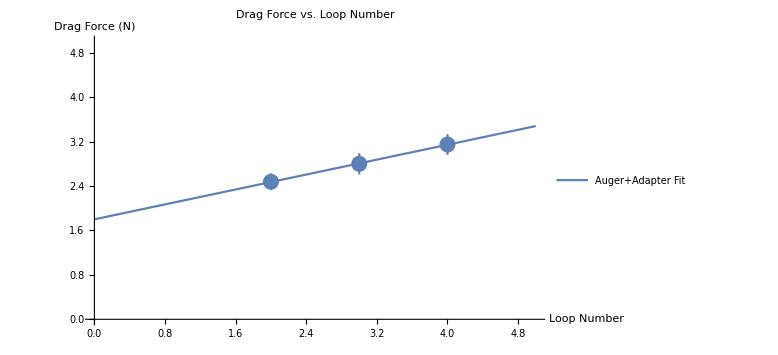

```mathematica
Show[{ErrorListPlot[{DataAugerFull}, PlotLabel->"Drag Force vs. Loop Number",PlotStyle-> PointSize[0.02],AxesLabel->{"Loop Number","Drag Force (N)"},ImageSize->Large, PlotRange->{{0,5},{0,5}}],Plot[{fitAuger},{x,0,5},PlotRange->{{0,5},{-1,6}},PlotLegends-> {"Auger+Adapter Fit","AugerBot Fit"}]}]
```

### Auger Only and AugerBot Force Trends

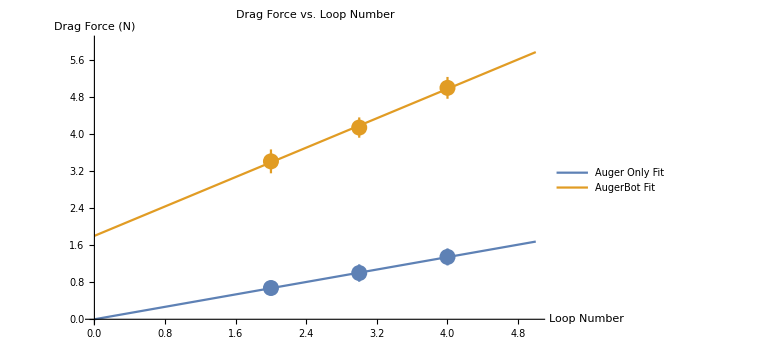

```mathematica
Show[{ErrorListPlot[{DataAugerAdjust, DataBotFull}, PlotLabel->"Drag Force vs. Loop Number",PlotStyle-> PointSize[0.02],AxesLabel->{"Loop Number","Drag Force (N)"},ImageSize->Large, PlotRange->{{0,5},{0,6}}],Plot[{fitAdjust, fitBot}, {x,0,5},PlotLegends-> {"Auger Only Fit","AugerBot Fit"}]}]
```

```mathematica
Print["Avg Motor Capsule Fd = ",avgMotorN, ", Sd = ", sdMotorN]
```

Avg Motor Capsule Fd = 3.80138, Sd = 0.24525

### Feedback

Good that the plot is linear. 
	Expect F_d to be linearly dependent on depth & coil #
	
Concerns 
	y-intercept drag force | Paul: Seems bit big at 1.8N. (Not sure where Paul’s intuition is coming into play here, since Fd varies with depth.)
	From just poking the robot around in the seeds, obvious F_d > F_x
	
Questions
	Why is the full robot trend not parallel? Attaching same body...so additional drag should be the same
		Because can’t see, possible I’m not burying it consistently at same depth. (Not sure how big of an affect this has.)
		Also possible that the packing factor differs enough to make a difference. 
		(Measuring after 3 pulls approximately because I don’t know the range. But this causes the front material to become more compact) 
		Had to use only the red adapter; green ones aren’t a tight fit. Shouldn’t be a concern because all made of PLA and the diameter and thickness is same.

Testing fixes: (Postponing future tests like this)
	Put a piece of tape on side of tank to mark consistent surface height and device depth. 
	Use a “leveler” to make sure bottom of trench is flat. (So robot is actually pulled in +x and not diagonally.)

```mathematica
(*With Paul During 9/26 Meeting*)
```

Clipping the wings reduced F_d. Thrust actually tangible. But not strong. Also, more spinning. 

Next
	Try more loops over increasing length of helix to increase F_x
	Make shorter wings - let’s try rectangular for now
	Add a cone at the base of the helix to reduce the blunt edge

## Modified Francisco Calculations : 10/18 (Do not use!)

```mathematica
Fx[α_,β_,ξ_,b_,c_]:=α*(β*b-ξ*c);
```

```mathematica
α = 2*Pi*N/Cos[ϕ];
β = (Cn-Ct)*w*Sin[ϕ]*Cos[ϕ];
ξ = u*(Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2);

(*Solved integrals by hand - don't like Mathematica's simplified output*)
b = (R/(2*w^2))*Sqrt[(R*w)^2+u^2]+(u^2/(2*w^3))*(Log[u]-Log[R*w+Sqrt[(R*W)^2+u^2]]); 
c = (1/w^2)*(Sqrt[(R*w)^2+u^2]-u);

thrust = Fx[α,β,ξ,b,c]
```

2 N π Sec[ϕ] ((Cn-Ct) w Cos[ϕ] ((R √(u^2+R^2 w^2))/(2 w^2)+(u^2 (Log[u]-Log[R w+√(u^2+R^2 W^2)]))/(2 w^3)) Sin[ϕ]-(u (-u+√(u^2+R^2 w^2)) (Cn Cos[ϕ]^2+Ct Sin[ϕ]^2))/w^2)

## Plotting Fx to find U which Balances Forces: 11/1

```mathematica
Quit;
```

### Parameters

#### For Helix

```mathematica
(*Current param: R = 1.8cm, ϕ = 5.4763645 deg, n = 3.5*)
R = 0.018; (*Screw radius, m*)
n = 3.5; (*Number of helix turns*)
```

#### For Material

```mathematica
zlpPoppy = 0.05; zcpPoppy = 0.5/6; zlpGlass = 0.05; zcpGlass = 0.1;  (*N/cm^3*)
xlpPoppy=0.0875; xcpPoppy = 0.125; xlpGlass = 0.1*(7/8); xcpGlass = 0.125;  (*N/cm^3*)

(*For screw with ϕ = 5.4763645 deg*)
αz = zlpGlass*(100^3); (*Vertical stress per unit depth, N/m^3*)
αx = xlpGlass*(100^3); (*Horizontal stress per unit depth, N/m^3*)

d = 0.05;(*Depth robot buried, m*)

(*Friction coefficients*)
Cn = αz*d; (*N/m^2*)
Ct = αx*d;
```

#### For Motor

```mathematica
w = 2*1000*(2*Pi)/3584;(*Angular velocity with 12V source, rad/s*)
```

(2 ticks/ms)*(1000 ms/s)*(2*Pi rad/rev)*(1 rev/3584 ticks)

### Thrust Equation

one = 2*Pi*n/Cos[ϕ];
two = (Cn - Ct)*w*Sin[ϕ]*Cos[ϕ];
three = (R/(2*w^2))*Sqrt[(R*w)^2 + U^2];
four = (U^2/(2*w^3))*(Log[U] - Log[R*w + Sqrt[(R*w)^2 + U^2]]);
five = U*(Ct*Sin[ϕ]^2 + Cn*Cos[ϕ]^2)*(Sqrt[(R*w)^2 + U^2] - U)/w^2;
Fx = one*(two*(three + four) - five);

```mathematica
Thrust[U_]:= (2*Pi*n/Cos[ϕ])*(((Cn-Ct)*w*Sin[ϕ]*Cos[ϕ])*(((R/(2*w^2))*Sqrt[(R*w)^2+U^2])+((U^2/(2*w^3))*(Log[U]-Log[R*w + Sqrt[(R*w)^2+U^2]])))-(U*(Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2)*(Sqrt[(R*w)^2+U^2]-U)/w^2));
```

### Plotting Thrust as a Function of U

```mathematica
ϕ = 5*Pi/180//N (*Pitch angle, radians*)
```

0.0872665

Let ϕ = 0.00174533

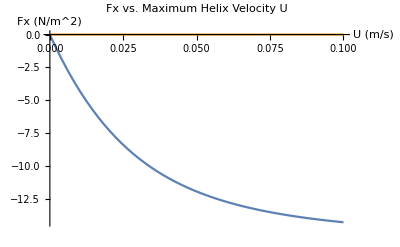

Let ϕ = 0.00349066

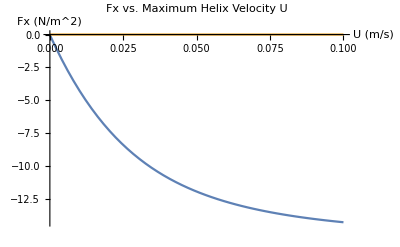

Let ϕ = 0.00523599

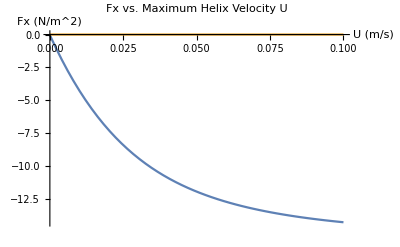

Let ϕ = 0.00698132

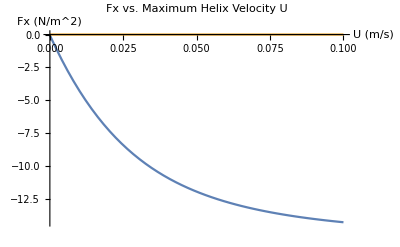

Let ϕ = 0.00872665

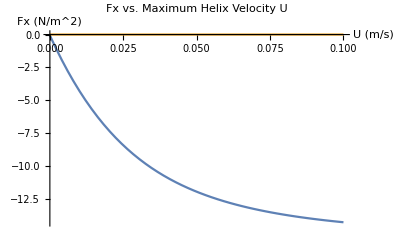

Let ϕ = 0.010472

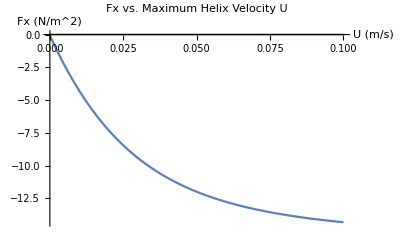

Let ϕ = 0.0122173

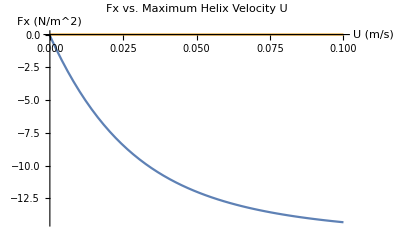

Let ϕ = 0.0139626

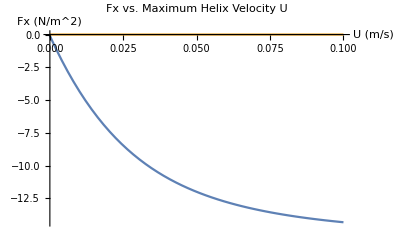

Let ϕ = 0.015708

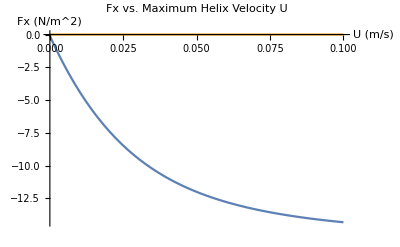

Let ϕ = 0.0174533

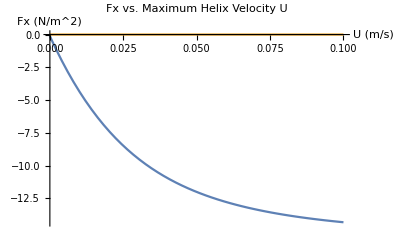

Let ϕ = 0.0191986

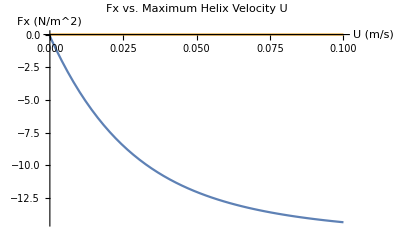

Let ϕ = 0.020944

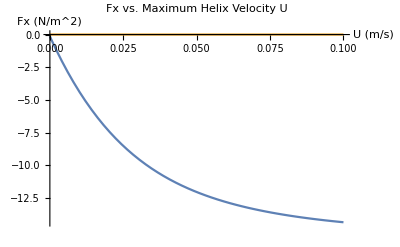

Let ϕ = 0.0226893

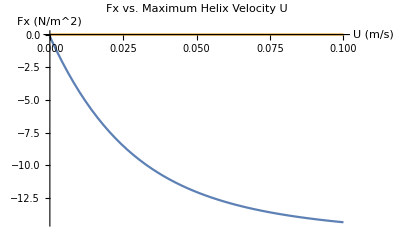

Let ϕ = 0.0244346

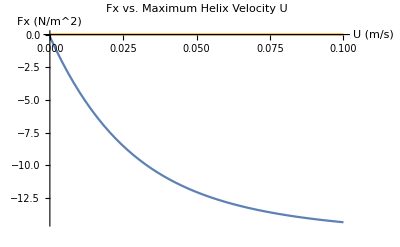

Let ϕ = 0.0261799

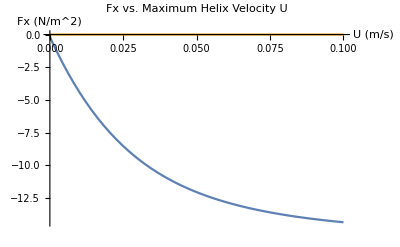

Let ϕ = 0.0279253

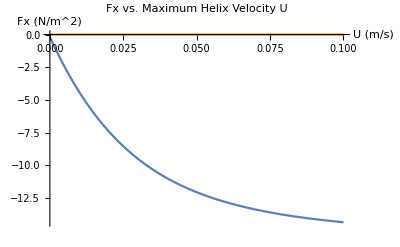

Let ϕ = 0.0296706

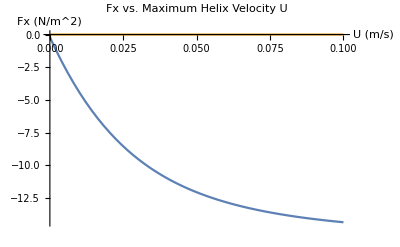

Let ϕ = 0.0314159

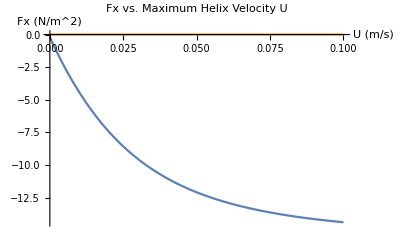

Let ϕ = 0.0331613

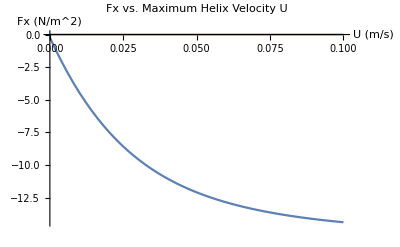

Let ϕ = 0.0349066

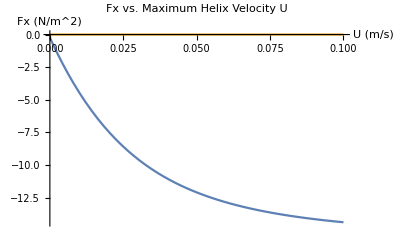

Let ϕ = 0.0366519

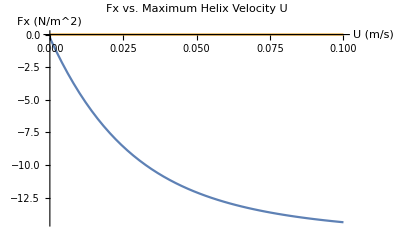

Let ϕ = 0.0383972

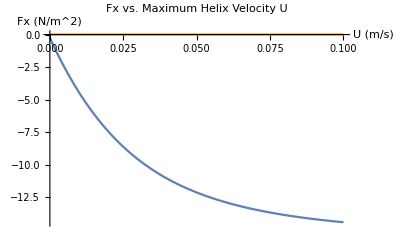

Let ϕ = 0.0401426

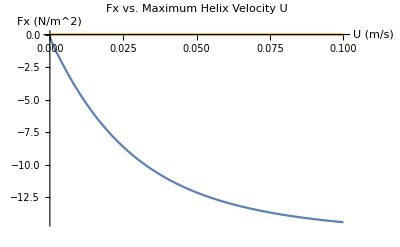

Let ϕ = 0.0418879

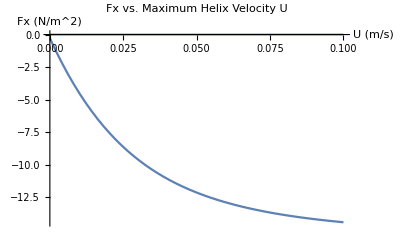

Let ϕ = 0.0436332

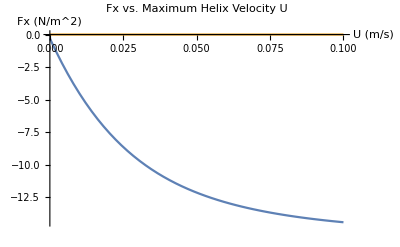

Let ϕ = 0.0453786

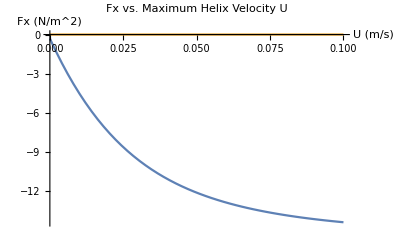

Let ϕ = 0.0471239

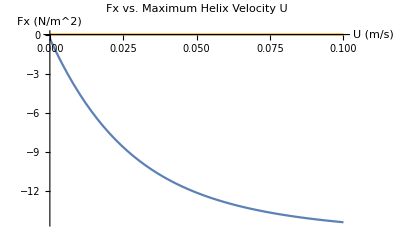

Let ϕ = 0.0488692

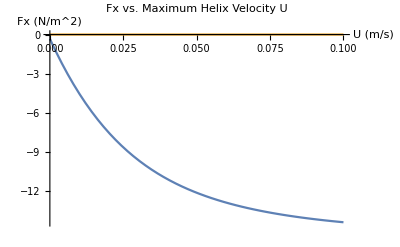

Let ϕ = 0.0506145

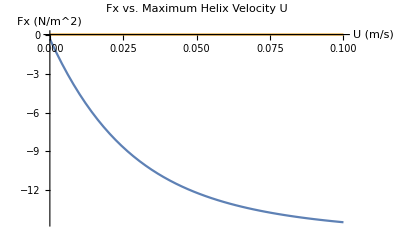

Let ϕ = 0.0523599

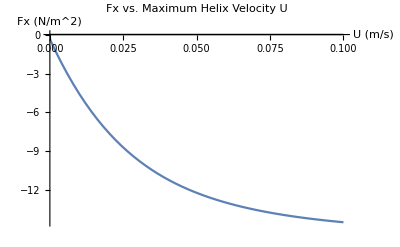

Let ϕ = 0.0541052

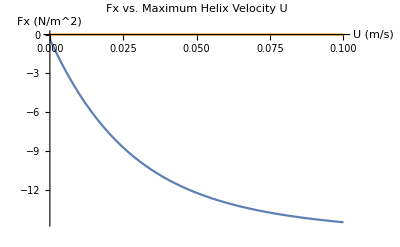

Let ϕ = 0.0558505

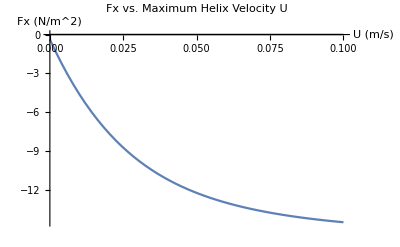

Let ϕ = 0.0575959

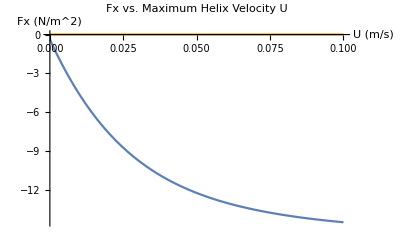

Let ϕ = 0.0593412

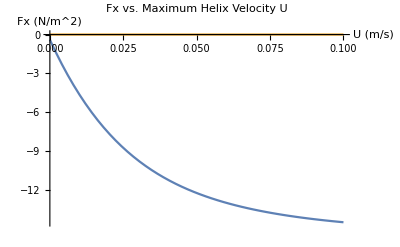

Let ϕ = 0.0610865

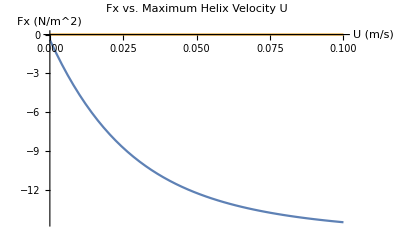

Let ϕ = 0.0628319

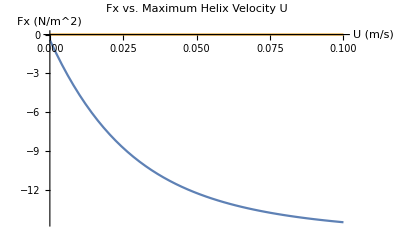

Let ϕ = 0.0645772

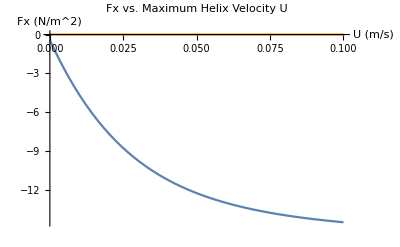

Let ϕ = 0.0663225

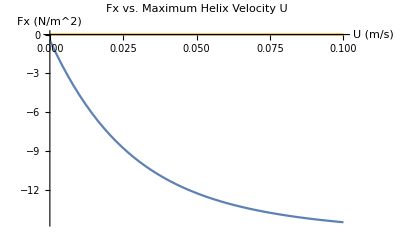

Let ϕ = 0.0680678

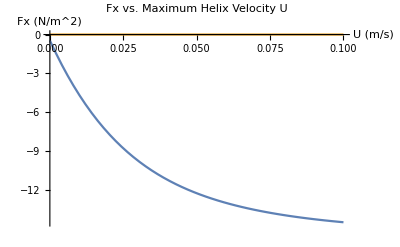

Let ϕ = 0.0698132

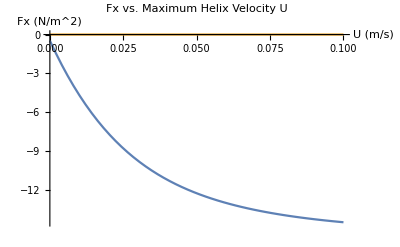

Let ϕ = 0.0715585

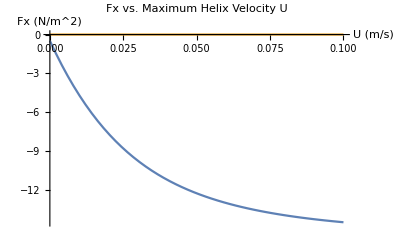

Let ϕ = 0.0733038

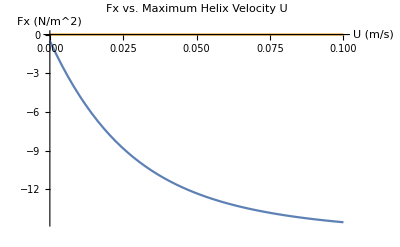

Let ϕ = 0.0750492

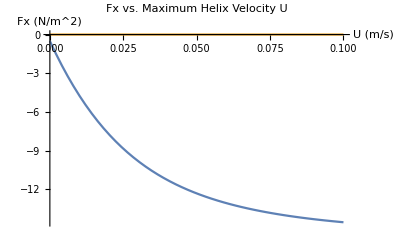

Let ϕ = 0.0767945

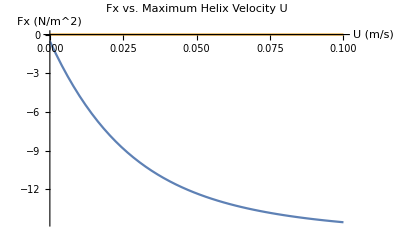

Let ϕ = 0.0785398

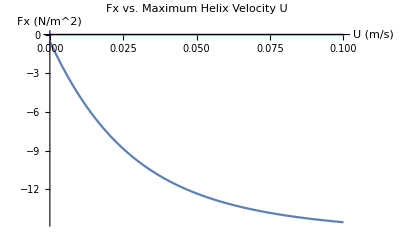

Let ϕ = 0.0802851

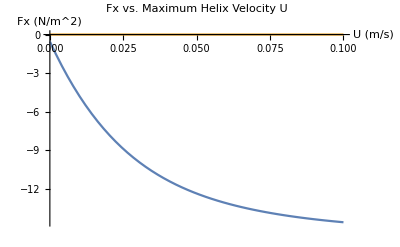

Let ϕ = 0.0820305

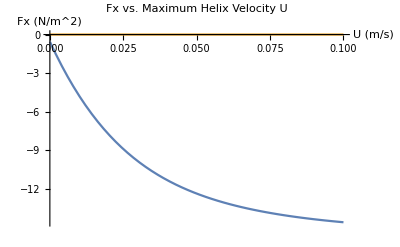

Let ϕ = 0.0837758

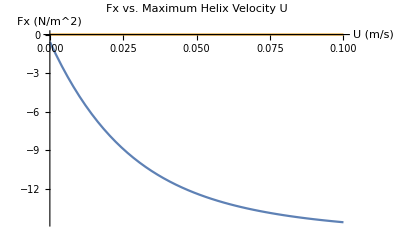

Let ϕ = 0.0855211

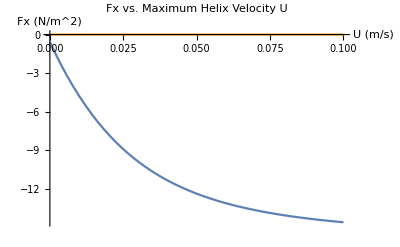

```mathematica
While[ϕ < 5*Pi/180,
Print["Let ϕ = ",ϕ];
Print@Plot[{Thrust[U],0},{U,0,0.1}, PlotLabel->"Fx vs. Maximum Helix Velocity U", AxesLabel->{"U (m/s)","Fx (N/m^2)"}, PlotRange->All];
ϕ = ϕ+(0.1*Pi/180);
]
```

## Plotting Fx to find U which Balances Forces 2 : 11/9

```mathematica
Quit;
```

Corrected packing factor chart measurements

Checked behavior of Fx equation

Non-dimensionalized Fx equation

## Finding Possible Case

### Parameters

#### For Helix

```mathematica
(*Current param: R = 1.8cm, n = 3.5*)
R = 0.018; (*Screw radius, m*)
n = 3.5; (*Number of helix turns*)
```

#### For Material

```mathematica
(*S5 and S6: 
az(β,γ) = az(0,sgn(zdot)*π/2)*|Cos[β]|, Approx Fz on horiz projection
 ax(β,γ) = ax(π/2,0)*|Sin[β]|, Approx Fx on vert projection 
*)

(*NOT SURE IF ZDOT IS + OR -, IF - THEN ALL Z VALUES UNDER AROUND 0*)
zlpPoppy=0.35;zcpPoppy=0.55;zlpGlass=0.3;zcpGlass=0.4;zcpGLASS = 0.3;(*az(0,sgn(zdot)*π/2), N/cm^3*)
xlpPoppy = 0.0625;xcpPoppy = 0.2/3;zlpGlass = 0.075;zcpGlass = 0.1;zcpGLASS = 0.0625;(*ax(π/2,0), N/cm^3*)

β = (Pi/2)-ϕ; (*ϕ is symbolic, radians*)
αz = zlpPoppy*Abs[Cos[β]]*(100^3); (*Vertical stress per unit depth, N/m^3*)
αx = xlpPoppy*Abs[Sin[β]]*(100^3); (*Horizontal stress per unit depth, N/m^3*)

d = 0.05;(*Depth robot buried, m*)

(*Friction coefficients, expressed in terms of ϕ*)
Cn = αz*d; (*N/m^2*)
Ct = αx*d;
```

#### For Motor

```mathematica
w = 2*1000*(2*Pi)/3584;(*Angular velocity with 12V source, rad/s*)
```

(2 ticks/ms)*(1000 ms/s)*(2*Pi rad/rev)*(1 rev/3584 ticks)

### Thrust Equation

```mathematica
Thrust[U_]:= (2*Pi*n/Cos[ϕ])*(((Cn-Ct)*w*Sin[ϕ]*Cos[ϕ])*(((R/(2*w^2))*Sqrt[(R*w)^2+U^2])+((U^2/(2*w^3))*(Log[U]-Log[R*w + Sqrt[(R*w)^2+U^2]])))-(U*(Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2)*(Sqrt[(R*w)^2+U^2]-U)/w^2));
```

```mathematica
NDThrust[u_]:= (2*Pi*R^2*n/Cos[ϕ])*(0.5*(Cn-Ct)*Sin[ϕ]*Cos[ϕ]*(Sqrt[1+u^2]+u^2*Log[u/(1+Sqrt[1+u^2])])-u*(Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2)*(Sqrt[1+u^2]-u));
```

#### Behavior Plots

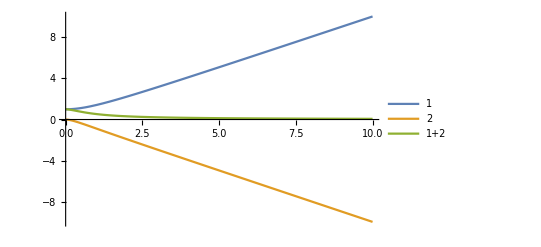

```mathematica
(*Term 1*)
test1 = Sqrt[1+u^2];test2 = u^2*Log[u/(1+Sqrt[1+u^2])];
Plot[{test1,test2,test1+test2},{u,0,10}, PlotLegends->{"1","2","1+2"}]
```

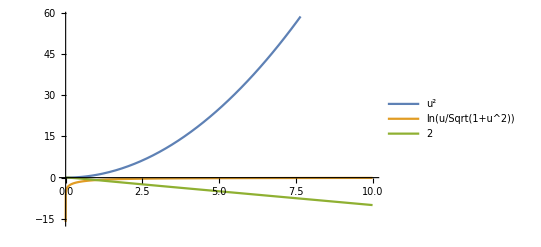

```mathematica
Plot[{u^2,Log[u/(1+Sqrt[1+u^2])],test2},{u,0,10},PlotLegends->{"u^2","ln(u/Sqrt(1+u^2))","2"}]
```

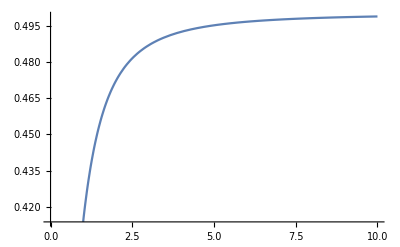

```mathematica
(*Term 2*)
test3 = u*(Sqrt[1+u^2]-u);
Plot[test3,{u,0,10}]
```

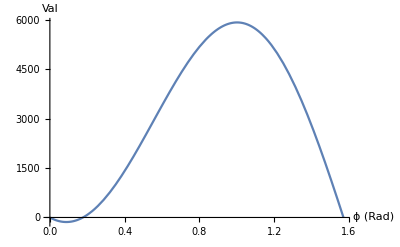

```mathematica
(*Friction coefficient terms: Quit and just run material parameters section*)
test4 =(Cn-Ct)*Sin[ϕ]*Cos[ϕ];
Plot[test4,{ϕ,0,Pi/2},AxesLabel->{"ϕ (Rad)","Val"}]
```

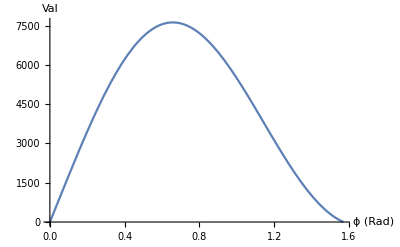

```mathematica
test5 = Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2;
Plot[test5,{ϕ,0,Pi/2},AxesLabel->{"ϕ (Rad)","Val"}]
```

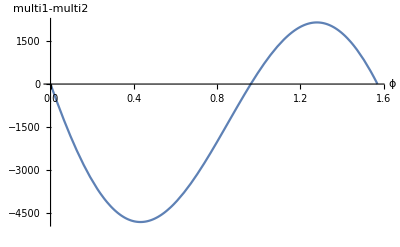

```mathematica
Plot[test4-test5,{ϕ,0,Pi/2},AxesLabel->{"ϕ","multi1-multi2"}]
```

### Plotting Thrust as a Function of U

```mathematica
ϕ = 10*Pi/180//N (*Local inclination, radians*)
```

0.174533

Let ϕ = 10. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = -6.61486

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 3040.01

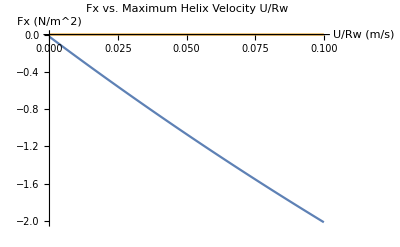

Let ϕ = 11. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 50.8664

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 3329.27

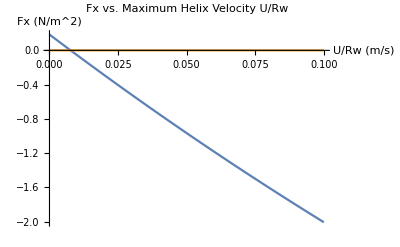

Let ϕ = 12. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 118.308

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 3613.31

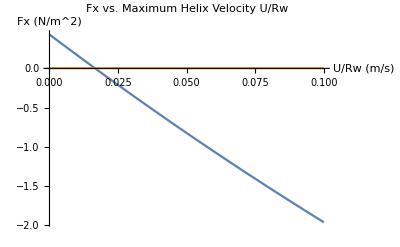

Let ϕ = 13. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 195.456

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 3891.52

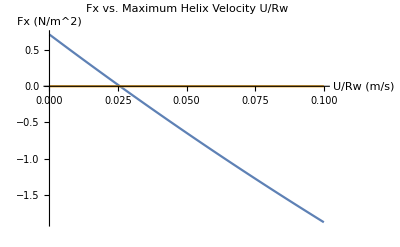

Let ϕ = 14. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 282.025

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 4163.32

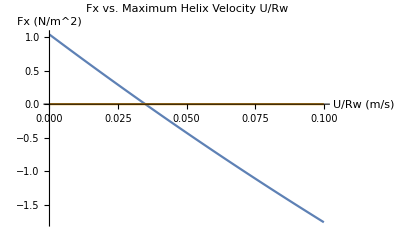

Let ϕ = 15. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 377.704

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 4428.13

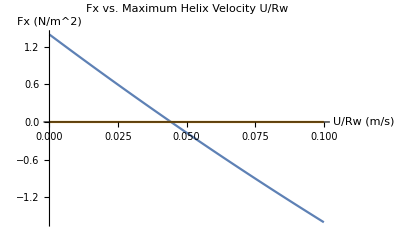

Let ϕ = 16. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 482.15

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 4685.4

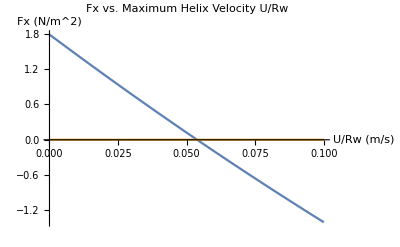

Let ϕ = 17. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 594.996

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 4934.6

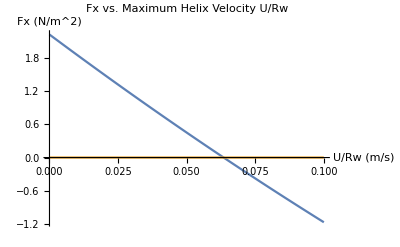

Let ϕ = 18. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 715.848

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 5175.2

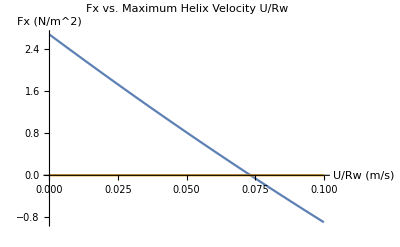

Let ϕ = 19. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 844.286

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 5406.73

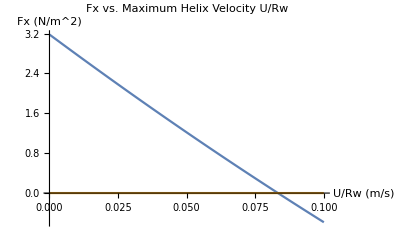

Let ϕ = 20. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 979.87

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 5628.71

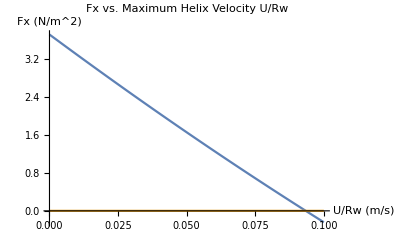

Let ϕ = 21. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 1122.13

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 5840.69

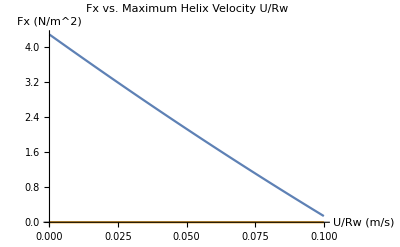

Let ϕ = 22. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 1270.59

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 6042.26

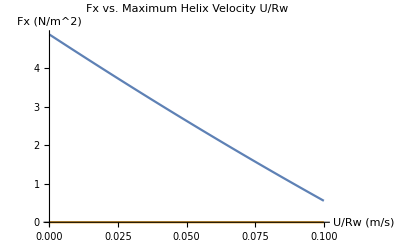

Let ϕ = 23. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 1424.73

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 6233.03

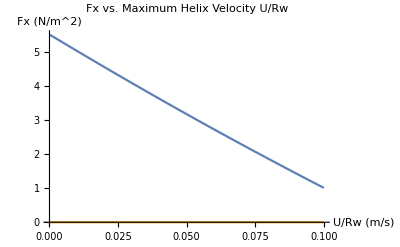

Let ϕ = 24. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 1584.04

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 6412.63

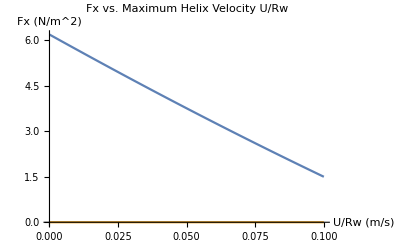

Let ϕ = 25. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 1747.96

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 6580.73

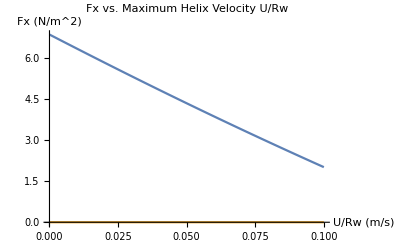

Let ϕ = 26. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 1915.96

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 6737.02

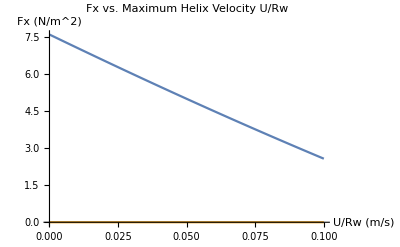

Let ϕ = 27. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 2087.44

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 6881.23

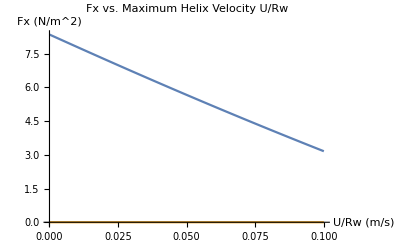

Let ϕ = 28. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 2261.84

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7013.11

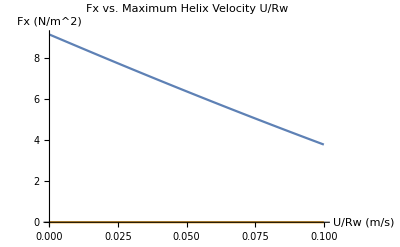

Let ϕ = 29. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 2438.55

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7132.46

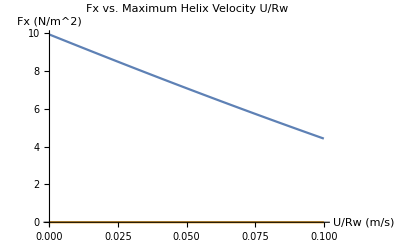

Let ϕ = 30. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 2616.99

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7239.08

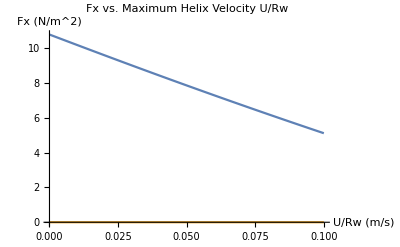

Let ϕ = 31. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 2796.52

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7332.85

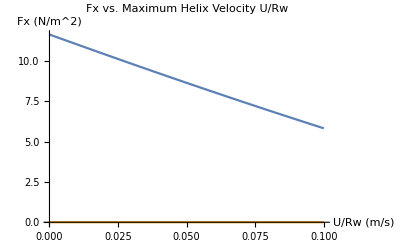

Let ϕ = 32. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 2976.55

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7413.63

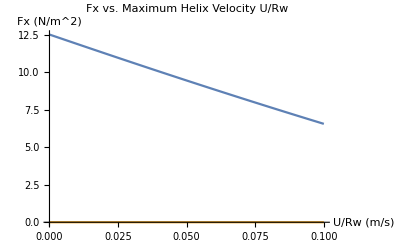

Let ϕ = 33. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 3156.45

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7481.36

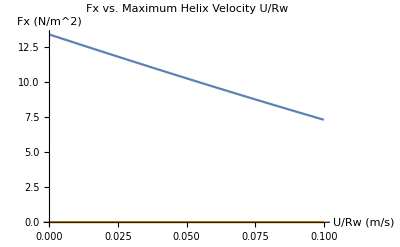

Let ϕ = 34. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 3335.61

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7535.98

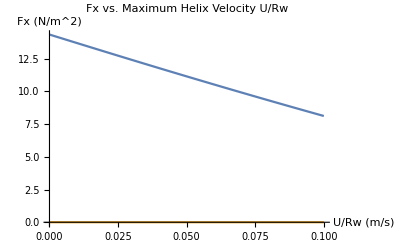

Let ϕ = 35. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 3513.39

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7577.49

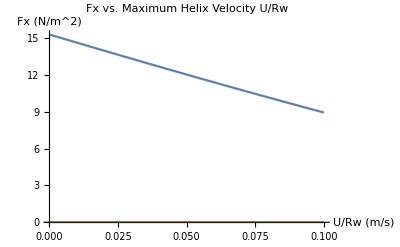

Let ϕ = 36. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 3689.18

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7605.9

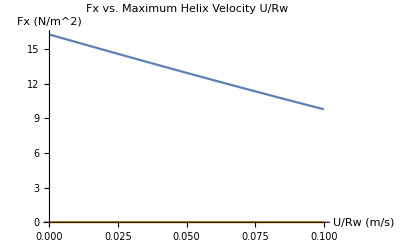

Let ϕ = 37. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 3862.36

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7621.26

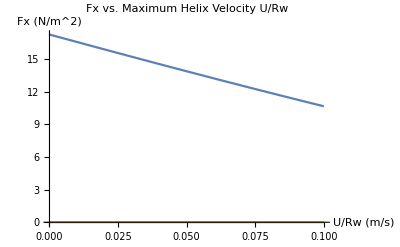

Let ϕ = 38. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 4032.33

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7623.68

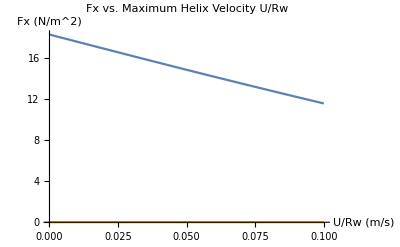

Let ϕ = 39. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 4198.47

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7613.26

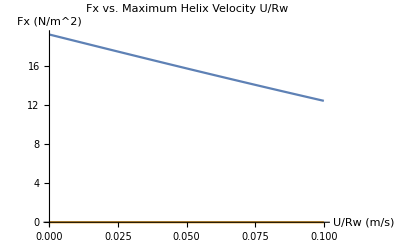

Let ϕ = 40. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 4360.18

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7590.15

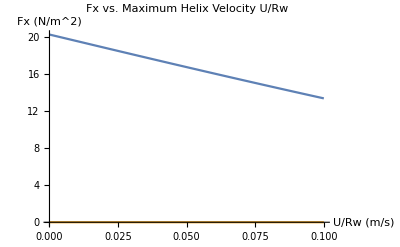

Let ϕ = 41. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 4516.89

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7554.56

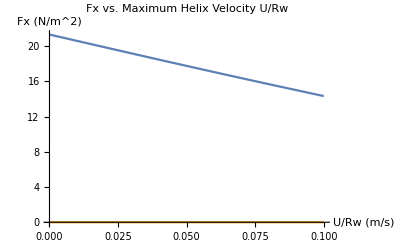

Let ϕ = 42. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 4668.02

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7506.68

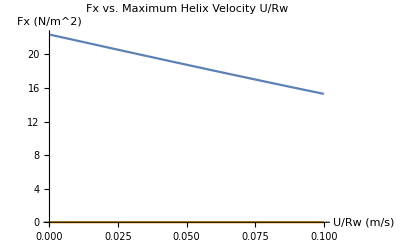

Let ϕ = 43. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 4812.99

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7446.78

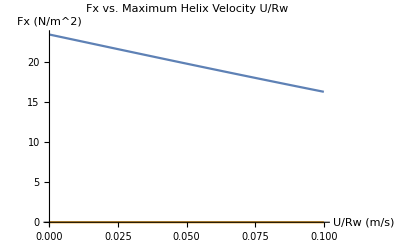

Let ϕ = 44. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 4951.27

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7375.13

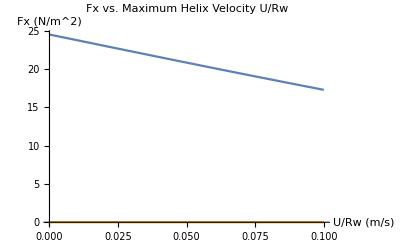

Let ϕ = 45. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5082.33

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7292.04

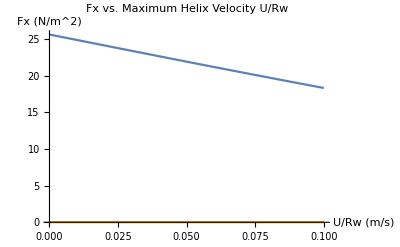

Let ϕ = 46. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5205.65

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7197.84

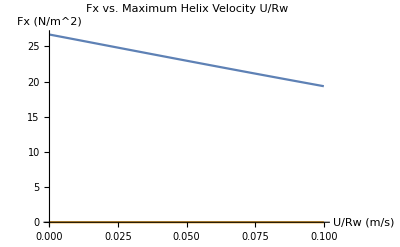

Let ϕ = 47. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5320.73

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 7092.91

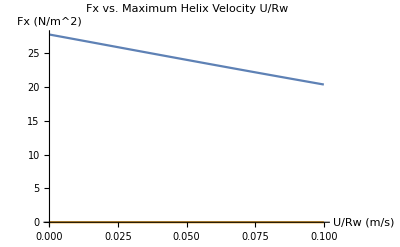

Let ϕ = 48. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5427.11

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 6977.62

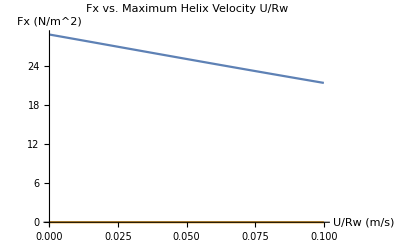

Let ϕ = 49. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5524.33

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 6852.41

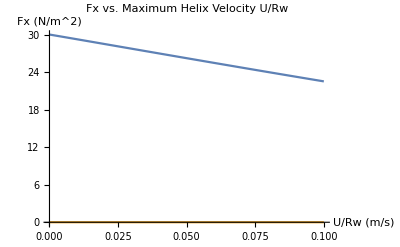

Let ϕ = 50. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5611.96

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 6717.7

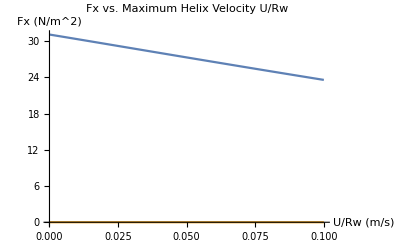

Let ϕ = 51. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5689.6

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 6573.98

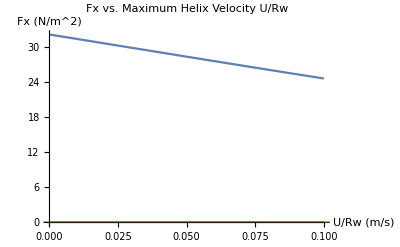

Let ϕ = 52. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5756.88

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 6421.71

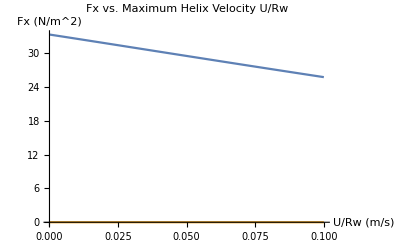

Let ϕ = 53. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5813.45

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 6261.42

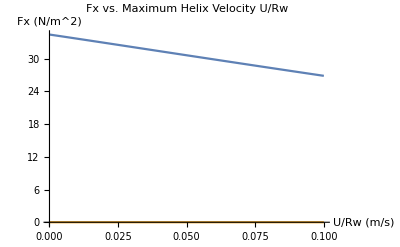

Let ϕ = 54. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5858.97

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 6093.62

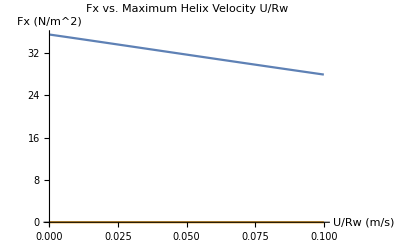

Let ϕ = 55. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5893.16

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 5918.86

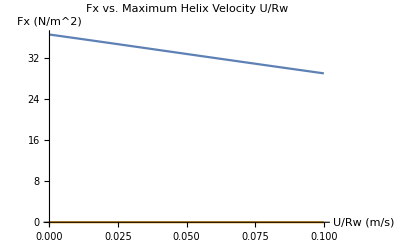

Let ϕ = 56. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5915.75

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 5737.7

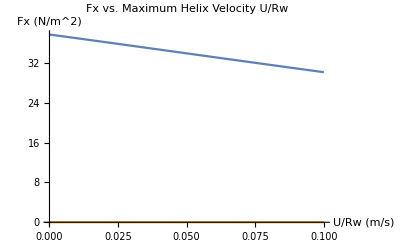

Let ϕ = 57. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5926.51

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 5550.72

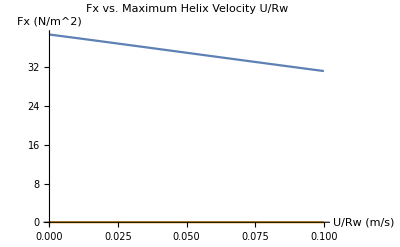

Let ϕ = 58. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5925.23

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 5358.49

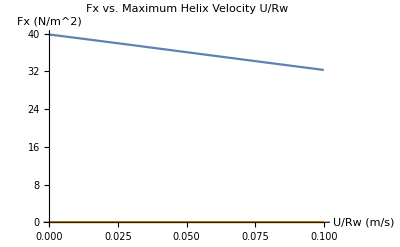

Let ϕ = 59. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5911.75

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 5161.63

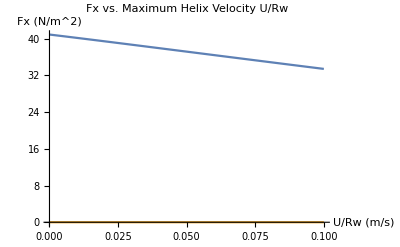

Let ϕ = 60. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5885.92

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 4960.74

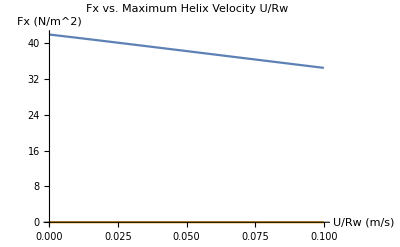

Let ϕ = 61. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5847.64

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 4756.43

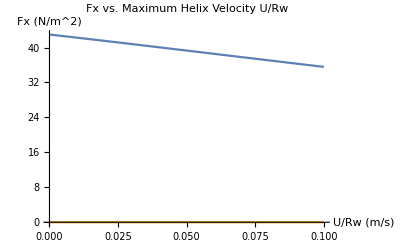

Let ϕ = 62. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5796.83

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 4549.33

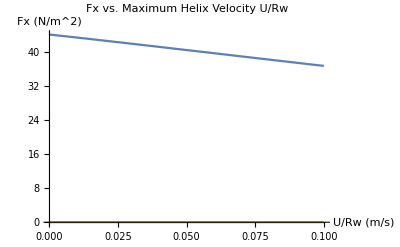

Let ϕ = 63. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5733.46

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 4340.06

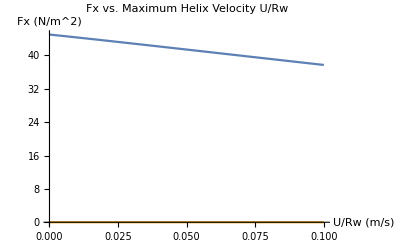

Let ϕ = 64. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5657.52

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 4129.27

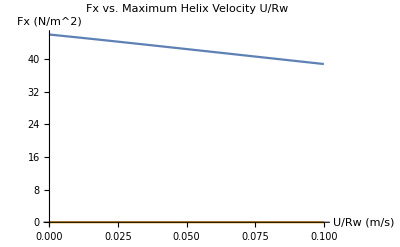

Let ϕ = 65. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5569.03

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 3917.56

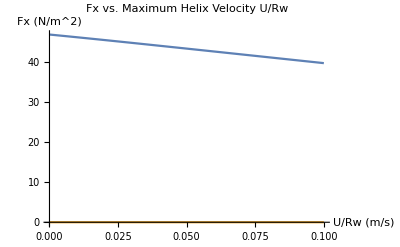

Let ϕ = 66. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5468.06

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 3705.59

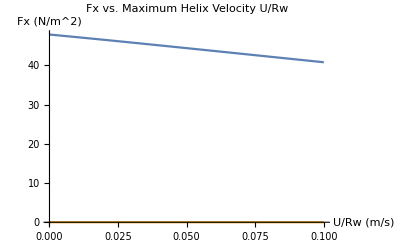

Let ϕ = 67. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5354.69

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 3493.97

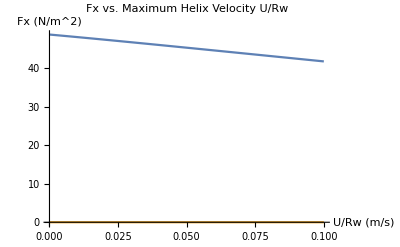

Let ϕ = 68. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5229.07

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 3283.33

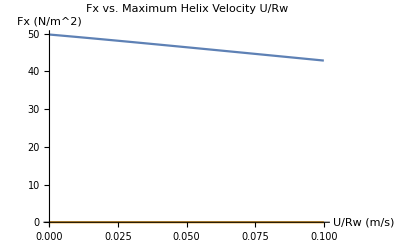

Let ϕ = 69. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 5091.33

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 3074.28

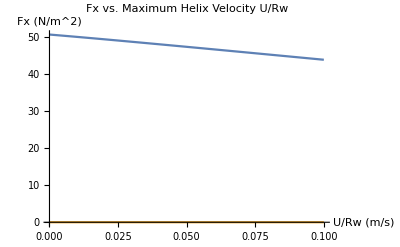

Let ϕ = 70. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 4941.69

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 2867.44

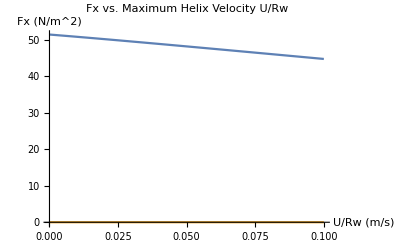

Let ϕ = 71. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 4780.36

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 2663.41

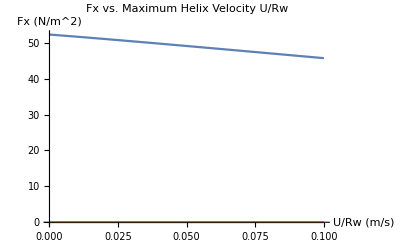

Let ϕ = 72. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 4607.59

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 2462.78

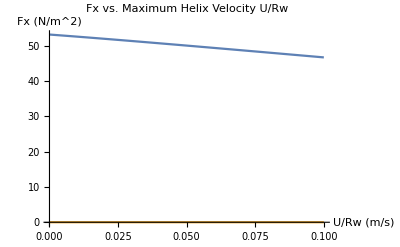

Let ϕ = 73. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 4423.68

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 2266.12

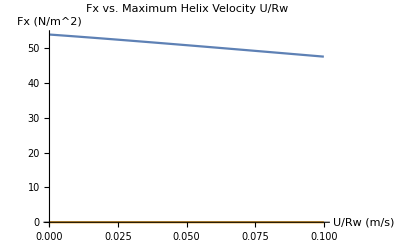

Let ϕ = 74. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 4228.94

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 2074.

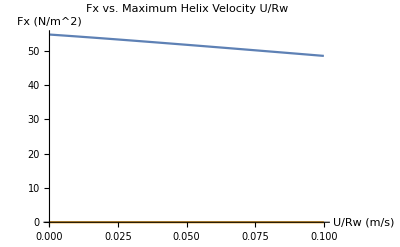

Let ϕ = 75. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 4023.72

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 1886.96

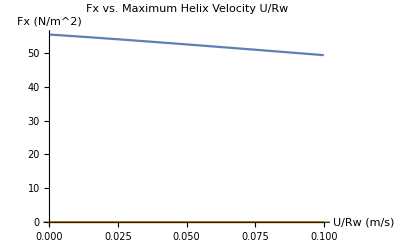

Let ϕ = 76. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 3808.39

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 1705.54

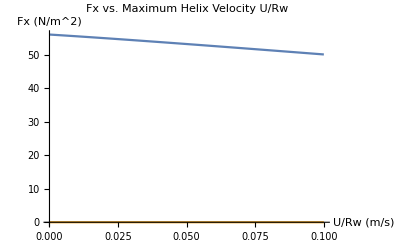

Let ϕ = 77. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 3583.36

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 1530.26

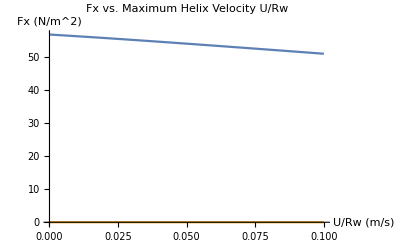

Let ϕ = 78. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 3349.04

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 1361.58

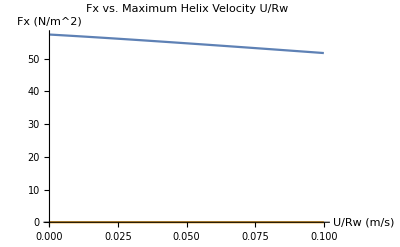

Let ϕ = 79. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 3105.9

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 1200.

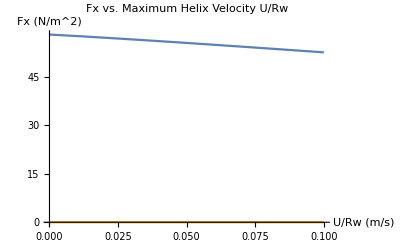

Let ϕ = 80. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 2854.41

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 1045.96

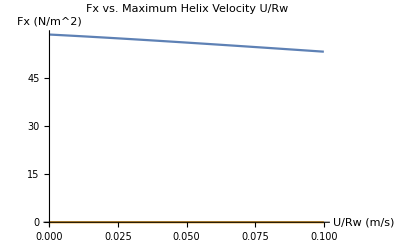

Let ϕ = 81. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 2595.08

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 899.877

-Graphics-

Let ϕ = 82. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 2328.42

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 762.153

-Graphics-

Let ϕ = 83. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 2054.97

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 633.16

-Graphics-

Let ϕ = 84. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 1775.3

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 513.243

-Graphics-

Let ϕ = 85. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 1489.99

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 402.719

-Graphics-

Let ϕ = 86. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 1199.63

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 301.875

-Graphics-

Let ϕ = 87. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 904.823

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 210.97

-Graphics-

Let ϕ = 88. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 606.193

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 130.23

-Graphics-

Let ϕ = 89. deg

(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = 304.372

Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = 59.8516

-Graphics-

```mathematica
While[ϕ < 90*Pi/180,
Print["Let ϕ = ",ϕ*180/Pi, " deg"];
Print["(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = ",(Cn-Ct)*Sin[ϕ]*Cos[ϕ]];
Print["Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = ",Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2];
Print@Plot[{NDThrust[u],0},{u,0,0.1}, PlotLabel->"Fx vs. Maximum Helix Velocity U/Rw", AxesLabel->{"U/Rw (m/s)","Fx (N/m^2)"}, PlotRange->All];
ϕ = ϕ+(1*Pi/180) (*Increment by 0.1 deg*)
]
```

## Inside Equation for Thrust: 11/16

```mathematica
Quit;
```

## Testing Model

### Parameters

#### For Helix

```mathematica
(*Current param: R = 1.8cm, n = 3.5*)
R = 0.018; (*Screw radius, m*)
n = 3.5; (*Number of helix turns*)
```

#### For Material

```mathematica
(*S5 and S6: 
az(β,γ) = az(0,sgn(zdot)*π/2)*|Cos[β]|, Approx Fz on horiz projection
 ax(β,γ) = ax(π/2,0)*|Sin[β]|, Approx Fx on vert projection 
*)

(*NOT SURE IF ZDOT IS + OR -, IF - THEN ALL Z VALUES UNDER AROUND 0*)
zlpPoppy=0.35;zcpPoppy=0.55;zlpGlass=0.3;zcpGlass=0.4;zcpGLASS = 0.3;(*az(0,sgn(zdot)*π/2), N/cm^3*)
xlpPoppy = 0.0625;xcpPoppy = 0.2/3;xlpGlass = 0.075;xcpGlass = 0.1;xcpGLASS = 0.0625;(*ax(π/2,0), N/cm^3*)

β = (Pi/2)-ϕ; (*ϕ is symbolic, radians*)
αz = zlpPoppy*Abs[Cos[β]]*(100^3); (*Vertical stress per unit depth, N/m^3*)
αx = xlpPoppy*Abs[Sin[β]]*(100^3); (*Horizontal stress per unit depth, N/m^3*)

d = 0.05;(*Depth robot buried, m*)

(*Friction coefficients, expressed in terms of ϕ*)
Cn = αz*d; (*N/m^2*)
Ct = αx*d;
```

#### For Motor

```mathematica
w =  2*1000*(2*Pi)/3584;(*Angular velocity with 12V source, rad/s*)
```

(2 ticks/ms)*(1000 ms/s)*(2*Pi rad/rev)*(1 rev/3584 ticks)

### Horizontal Thrust Inner Equation

```mathematica
FxIn[u_]:=(0.5*(Cn-Ct)*Sin[ϕ]*Cos[ϕ]*(Sqrt[1+u^2]+u^2*Log[u/(1+Sqrt[1+u^2])])-u*(Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2)*(Sqrt[1+u^2]-u));
```

ϕ input must be in radians

### Calculating U/Rw when Fx = 0 for Many ϕ Cases

```mathematica
ϕ = 15*Pi/180//N; (*Local inclination, radians*)
ϕstore = {};
ustore = {};
Fstore = {};
FMaxstore = {}; (*FxIn when u = 0.001*)
```

```mathematica
(*Finding U/Rw Intercepts*)
While[ϕ < 90*Pi/180,
(*Print statements*)
(*Print["Let ϕ = ",ϕ*180/Pi, " deg"];
Print["(Cn-Ct)*Sin[ϕ]*Cos[ϕ] = ",(Cn-Ct)*Sin[ϕ]*Cos[ϕ]];
Print["Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2 = ",Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2];*)
(*Print@Plot[{FxIn[u],0},{u,0,0.1}, PlotLabel->"Inner Fx vs. Helix Velocity U/Rw", AxesLabel->{"U/Rw (m/s)","Fx (N/m^2)"}, PlotRange->All];*)

(*Finding U/Rw intercept: Newton-Raphson Method*)
guess = 0.01; (*Reset initial guess*)
grad = D[FxIn[u],u];
While[FxIn[guess]>10^-6, (*Keep iterating until FxIn ≃ 0*)
gradEval = grad/.u-> guess; (*Find FxIn'(guess)*)
guess = guess-FxIn[guess]/gradEval (*Subscript[u, i+1] = Subscript[u, i] - FxIn(Subscript[u, i])/FxIn'(Subscript[u, i])*)
];
uint = guess; (*U/Rw intercept found*)

(*Storing data in arrays*)
ϕstore = Join[ϕstore,{ϕ}]; (*Storing ϕ in Radians*)
FMaxstore = Join[FMaxstore, {FxIn[10^-3]}]; (*FxIn(0.001)*)
ustore = Join[ustore, {uint}]; (*U/Rw found when FxIn < 10^-6*)
Fstore = Join[Fstore, {FxIn[uint]}]; (*FxIn val at u-intercept*)

ϕ = ϕ+(1*Pi/180) (*Increment by 1 deg*)
]
```

### Analysis

```mathematica
ϕcol ={ϕstore}ᵀ;ucol ={ustore}ᵀ;Fcol = {Fstore}ᵀ;Fmaxcol = {FMaxstore}ᵀ;

(*Helix Translation Speed vs. Local Incline Angle ϕ*)
dataPlot =Join[ϕcol,ucol,2]; 
ListPlot[dataPlot, PlotLabel->"U/Rw vs ϕ", AxesLabel->{"ϕ (Rad)","U/Rw"}, ImageSize->Large]
```

-Graphics-

Should have a maximum.

```mathematica
(*FxIn Max vs. Local Incline Angle ϕ*)
dataMax = Join[ϕcol, Fmaxcol,2];
ListPlot[dataMax, PlotLabel->"FxIn Max vs. ϕ", AxesLabel->{"ϕ (Rad)","FxIn Max"}, ImageSize->Large, PlotRange->Full]
```

-Graphics-

```mathematica
(*Checking Data Values: ϕ is left col, U/Rw is right col*)
dataTable = Join[ϕcol,ucol,Fcol,2];
Grid[Join[{{"ϕ (Deg)",  "U/Rw", "FxIn[U/Rw]"}},dataTable,1]]
```

ϕ (Deg) | U/Rw | FxIn[U/Rw]
0.261799 | 0.0442894 | 3.55897×10^-9
0.279253 | 0.0538053 | 2.30265×10^-8
0.296706 | 0.0634723 | 1.036×10^-7
0.314159 | 0.0732932 | 3.64453×10^-7
0.331613 | 0.0832716 | 5.68434×10^-14
0.349066 | 0.0934114 | 5.68434×10^-14
0.366519 | 0.103717 | 1.13687×10^-13
0.383972 | 0.114193 | 0.
0.401426 | 0.124845 | 1.13687×10^-13
0.418879 | 0.135678 | 4.54747×10^-13
0.436332 | 0.146699 | 1.36424×10^-12
0.453786 | 0.157913 | 3.86535×10^-12
0.471239 | 0.169329 | 1.01181×10^-11
0.488692 | 0.180953 | 2.54659×10^-11
0.506145 | 0.192792 | 6.09361×10^-11
0.523599 | 0.204857 | 1.38243×10^-10
0.541052 | 0.217155 | 2.98769×10^-10
0.558505 | 0.229697 | 6.2164×10^-10
0.575959 | 0.242491 | 1.24646×10^-9
0.593412 | 0.255551 | 2.42062×10^-9
0.610865 | 0.268885 | 4.56021×10^-9
0.628319 | 0.282509 | 8.36349×10^-9
0.645772 | 0.296433 | 1.49571×10^-8
0.663225 | 0.310673 | 2.61371×10^-8
0.680678 | 0.325243 | 4.47076×10^-8
0.698132 | 0.34016 | 7.49646×10^-8
0.715585 | 0.355439 | 1.2339×10^-7
0.733038 | 0.3711 | 1.99614×10^-7
0.750492 | 0.387163 | 3.17728×10^-7
0.767945 | 0.403647 | 4.98091×10^-7
0.785398 | 0.420575 | 7.69727×10^-7
0.802851 | 0.437972 | -4.54747×10^-13
0.820305 | 0.455864 | -4.54747×10^-13
0.837758 | 0.474277 | -4.54747×10^-13
0.855211 | 0.493243 | 0.
0.872665 | 0.512794 | 4.54747×10^-13
0.890118 | 0.532964 | 0.
0.907571 | 0.553792 | 0.
0.925025 | 0.575319 | 4.54747×10^-13
0.942478 | 0.59759 | 0.
0.959931 | 0.620653 | 2.27374×10^-13
0.977384 | 0.644562 | 4.54747×10^-13
0.994838 | 0.669374 | 6.82121×10^-13
1.01229 | 0.695153 | 2.04636×10^-12
1.02974 | 0.721969 | 3.63798×10^-12
1.0472 | 0.749898 | 5.68434×10^-12
1.06465 | 0.779024 | 1.11413×10^-11
1.0821 | 0.809441 | 2.02363×10^-11
1.09956 | 0.841251 | 3.66072×10^-11
1.11701 | 0.874571 | 6.61657×10^-11
1.13446 | 0.909526 | 1.14824×10^-10
1.15192 | 0.946259 | 1.99179×10^-10
1.16937 | 0.984931 | 3.39924×10^-10
1.18682 | 1.02572 | 5.74346×10^-10
1.20428 | 1.06883 | 9.63837×10^-10
1.22173 | 1.11449 | 1.59594×10^-9
1.23918 | 1.16297 | 2.61389×10^-9
1.25664 | 1.21455 | 4.23711×10^-9
1.27409 | 1.26958 | 6.79756×10^-9
1.29154 | 1.32846 | 1.0794×10^-8
1.309 | 1.39165 | 1.69572×10^-8
1.32645 | 1.45967 | 2.63642×10^-8
1.3439 | 1.53316 | 4.05579×10^-8
1.36136 | 1.61285 | 6.17229×10^-8
1.37881 | 1.69962 | 9.28998×10^-8
1.39626 | 1.79452 | 1.38224×10^-7
1.41372 | 1.89883 | 2.03169×10^-7
1.43117 | 2.0141 | 2.94674×10^-7
1.44862 | 2.14226 | 4.20971×10^-7
1.46608 | 2.28569 | 5.90566×10^-7
1.48353 | 2.44742 | 8.09265×10^-7
1.50098 | 2.63133 | -2.84217×10^-13
1.51844 | 2.8425 | 2.84217×10^-13
1.53589 | 3.08767 | -5.18696×10^-13
1.55334 | 3.376 | -4.79616×10^-13

```mathematica
ϕ = ϕcol[[5,1]]
u0 = ucol[[5,1]]
FxIn[u0]
```

0.331613

0.0832716

5.68434×10^-14

## Backtracking: 11/27

Dimensionalized Fx to Nondimensionalized Fx ✓

## Francisco' s Eqn w/ Constant Ct, Cn, and N (turns)

```mathematica
Quit;
```

### Setup

```mathematica
(*Parameters from paper*)
r = 5/1000;w = 10.4;n = 3.5;
c = 24; d = 3/1000;ρ = 1.45*10^3;g = 9.8;h = 50/1000; 
Um = 0.11; ϕ0 = 16*Pi/180;
```

```mathematica
(*Solving for friction coefficients used in Figure 3 of Francisco's paper*)
eq1 = (CN/CT) - ((1+Um*Tan[ϕ0])/(1-Um/Tan[ϕ0]));
eq2 = CN-CT - c*d*ρ*g*h;
coeffSol = NSolve[{eq1 ==0, eq2 ==0}, {CT, CN}][[1]];
Ct = coeffSol[[1,2]]
Cn = coeffSol[[2,2]]
```

75.9513

127.107

```mathematica
(*Eq 2 - 10/21/17 | Parametrized f Integrated only wrt dθ*)
Fran[u_]:=(2*Pi*n*r/Cos[ϕ])*((Cn - Ct)*r*w*Sin[ϕ]*Cos[ϕ]-u*(Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2))/Sqrt[u^2+(r*w)^2];
```

### Calculating U/Rw when Fx = 0 for Many ϕ Cases

```mathematica
ϕ = 10*Pi/180//N; (*Local inclination, radians*)
ϕstore = {};
ustore = {};
Fstore = {};
FMaxstore = {}; (*FxIn when u = 0.001*)
```

```mathematica
(*Finding U/Rw intercepts*)
While[ϕ < 90*Pi/180,
(*Print statements*)
(*Print["Let ϕ = ",ϕ*180/Pi, " deg"];*)
(*Print@Plot[{Fran[u],0},{u,0,0.2}, PlotLabel->"Inner Fx vs. Helix Velocity U/Rw", AxesLabel->{"U/Rw (m/s)","Fx (N/m^2)"}, PlotRange->All];*)

(*Finding U/Rw intercept: Newton-Raphson Method*)
guess = 0.01; (*Reset initial guess*)
grad = D[Fran[u],u];
While[Fran[guess]>10^-6, (*Keep iterating until FxIn ≃ 0*)
gradEval = grad/.u-> guess; (*Find FxIn'(guess)*)
guess = guess-Fran[guess]/gradEval (*Subscript[u, i+1] = Subscript[u, i] - FxIn(Subscript[u, i])/FxIn'(Subscript[u, i])*)
];
uint = guess; (*U/Rw intercept found*)

(*Storing data in arrays*)
ϕstore = Join[ϕstore,{ϕ}]; (*Storing ϕ in Radians*)
FMaxstore = Join[FMaxstore, {Fran[10^-3]}]; (*FxIn(0.001)*)
ustore = Join[ustore, {uint}]; (*U/Rw found when FxIn < 10^-6*)
Fstore = Join[Fstore, {Fran[uint]}]; (*FxIn val at u-intercept*)

ϕ = ϕ+(1*Pi/180) (*Increment by 1 deg*)
]
```

### Plotting Data

```mathematica
ϕFcol ={ϕstore}ᵀ;uFcol ={ustore}ᵀ;

(*Helix Translation Speed vs. Local Incline Angle ϕ*)
dataPlot =Join[ϕFcol,uFcol,2]; 
ListPlot[dataPlot, PlotLabel->"U/Rw vs ϕ", AxesLabel->{"ϕ (Rad)","U/Rw"}, ImageSize->Large]
```

-Graphics-

When friction coefficients Ct and Cn are held constant, a maximum helix translational speed does occur. A significant increase in U/Rw starts around 28.6479 degrees.
Note: the number of turns (n) was kept the same. This means that the projected length of the helix along the x-axis is not constant.

## Francisco With Chen' s Coefficients

```mathematica
Quit;
```

```mathematica
(*Parameters from paper*)
r = 5/1000;w = 10.4;n = 3.5;

zlpGlass=0.3;xlpGlass = 0.075;
β = (Pi/2)-ϕ; (*ϕ is symbolic, radians*)
αz = zlpGlass*Abs[Cos[β]]*(100^3); (*Vertical stress per unit depth, N/m^3*)
αx = xlpGlass*Abs[Sin[β]]*(100^3); (*Horizontal stress per unit depth, N/m^3*)

d = 0.05;(*Depth robot buried, 50mm*)

(*Friction coefficients, expressed in terms of ϕ*)
Cn = αz*d; (*N/m^2*)
Ct = αx*d; 

(*Eq 2 - 10/21/17 | Parametrized f Integrated only wrt dθ*)
FranChen[u_]:=(2*Pi*n*r/Cos[ϕ])*((Cn - Ct)*r*w*Sin[ϕ]*Cos[ϕ]-u*(Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2))/Sqrt[u^2+(r*w)^2];
```

### Calculating U/Rw when Fx = 0 for Many ϕ Cases

```mathematica
ϕ = 10*Pi/180//N; (*Local inclination, radians*)
ϕstore = {};
ustore = {};
Fstore = {};
FMaxstore = {}; (*FxIn when u = 0.001*)
```

```mathematica
(*Finding U/Rw intercepts*)
While[ϕ < 90*Pi/180,
(*Print statements*)
(*Print["Let ϕ = ",ϕ*180/Pi, " deg"];*)
(*Print@Plot[{FranChen[u],0},{u,0,0.2}, PlotLabel->"Inner Fx vs. Helix Velocity U/Rw", AxesLabel->{"U/Rw (m/s)","Fx (N/m^2)"}, PlotRange->All];*)

(*Finding U/Rw intercept: Newton-Raphson Method*)
guess = 0.01; (*Reset initial guess*)
grad = D[FranChen[u],u];
While[FranChen[guess]>10^-6, (*Keep iterating until FxIn ≃ 0*)
gradEval = grad/.u-> guess; (*Find FxIn'(guess)*)
guess = guess-FranChen[guess]/gradEval (*Subscript[u, i+1] = Subscript[u, i] - FxIn(Subscript[u, i])/FxIn'(Subscript[u, i])*)
];
uint = guess; (*U/Rw intercept found*)

(*Storing data in arrays*)
ϕstore = Join[ϕstore,{ϕ}]; (*Storing ϕ in Radians*)
FMaxstore = Join[FMaxstore, {FranChen[10^-3]}]; (*FxIn(0.001)*)
ustore = Join[ustore, {uint}]; (*U/Rw found when FxIn < 10^-6*)
Fstore = Join[Fstore, {FranChen[uint]}]; (*FxIn val at u-intercept*)

ϕ = ϕ+(1*Pi/180) (*Increment by 1 deg*)
]
```

### Plotting Francisco - Chen Results

```mathematica
ϕFCcol ={ϕstore}ᵀ;uFCcol ={ustore}ᵀ;

(*Helix Translation Speed vs. Local Incline Angle ϕ*)
dataPlot =Join[ϕFCcol,uFCcol,2]; 
ListPlot[dataPlot, PlotLabel->"U/Rw vs ϕ", AxesLabel->{"ϕ (Rad)","U/Rw"}, ImageSize->Large]
```

-Graphics-

Evidently, Chen' s variable Ct and Cn coefficients mess with Francisco' s equation in a way which does not intuitively make sense.

## Francisco' s with Chen' s Coefficients: 11/30 (CORRECT ONES)

```mathematica
Quit;
```

## Francisco With Chen' s Coefficients

```mathematica
(*Parameters from paper*)
r = 5/1000;w = 10.4;n = 1;

(*LP poppy Fourier coefficients*)
A00 = 0.051; A10 = 0.047; B11 = 0.053; B01 = 0.083; Bn11 = 0.020; C11 = -0.026; C01 = 0.057; Cn11 = 0; D10 = 0.025;
```

```mathematica
β = (Pi/2)-ϕ; (*ϕ is symbolic, radians*)
αz = Bn11*Sin[2*Pi*(-β/Pi)] + A00*Cos[2*Pi*0]+B01*Sin[2*Pi*0]+A10*Cos[2*Pi*(β/Pi)]+B11*Sin[2*Pi*(β/Pi)]; (*Vertical stress per unit depth, N/m^3*)
αx = Cn11*Cos[2*Pi*(-β/Pi)]+C01*Cos[2*Pi*0]+D10*Sin[2*Pi*(β/Pi)]+C11*Cos[2*Pi*(β/Pi)]; (*Horizontal stress per unit depth, N/m^3*)

(*Friction coefficients, expressed in terms of ϕ*)
d = 0.05;(*Depth robot buried, 50mm*)
Cn = αx*d; (*N/m^2*)
Ct = αz*d; 

Cn/.ϕ -> 0
Ct/.ϕ-> 0
```

0.00415

0.0002

```mathematica
(*Eq 2 - 10/21/17 | Parametrized f Integrated only wrt dθ*)
FranChen[u_]:=(2*Pi*n*r/Cos[ϕ])*((Cn - Ct)*r*w*Sin[ϕ]*Cos[ϕ]-u*(Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2))/Sqrt[u^2+(r*w)^2];
```

### Calculating U/Rw when Fx = 0 for Many ϕ Cases

```mathematica
ϕ = 10*Pi/180//N; (*Local inclination, radians*)
ϕstore = {};
ustore = {};
Fstore = {};
FMaxstore = {}; (*FxIn when u = 0.001*)
```

```mathematica
(*Finding U intercepts*)
While[ϕ < 90*Pi/180,
(*Print statements*)
(*Print["Let ϕ = ",ϕ*180/Pi, " deg"];*)
(*Print@Plot[{FranChen[u],0},{u,0,0.2}, PlotLabel->"Inner Fx vs. Helix Velocity U/Rw", AxesLabel->{"U (m/s)","Fx (N/m^2)"}, PlotRange->All];*)

(*Finding U intercept: Newton-Raphson Method*)
guess = 0.001; (*Reset initial guess*)
grad = D[FranChen[u],u];
While[FranChen[guess]>10^-6, (*Keep iterating until FxIn ≃ 0*)
gradEval = grad/.u-> guess; (*Find FxIn'(guess)*)
guess = guess-FranChen[guess]/gradEval (*Subscript[u, i+1] = Subscript[u, i] - FxIn(Subscript[u, i])/FxIn'(Subscript[u, i])*)
];
uint = guess; (*U/Rw intercept found*)

(*Storing data in arrays*)
ϕstore = Join[ϕstore,{ϕ}]; (*Storing ϕ in Radians*)
FMaxstore = Join[FMaxstore, {FranChen[10^-3]}]; (*FxIn(0.001)*)
ustore = Join[ustore, {uint}]; (*U found when FxIn < 10^-6*)
Fstore = Join[Fstore, {FranChen[uint]}]; (*FxIn val at u-intercept*)

ϕ = ϕ+(1*Pi/180) (*Increment by 1 deg*)
]
```

### Plotting Francisco - Chen Results

```mathematica
ϕFCcol ={ϕstore}ᵀ;uFCcol ={ustore}ᵀ;

(*Helix Translation Speed vs. Local Incline Angle ϕ*)
dataPlot =Join[ϕFCcol,uFCcol,2]; 
ListPlot[dataPlot, PlotLabel->"U/Rw vs ϕ", AxesLabel->{"ϕ (Rad)","U (m/s)"}, ImageSize->Large]
```

-Graphics-

Using Chen’s Fourier coefficients does result in a maximum speed!!! Only phi values between 0 and 45 ° produce net forward thrust results!

## Testing Auger Model with Correct Chen Coefficients

### Parameters

#### For Helix

```mathematica
(*Current param: R = 1.8cm, n = 3.5*)
R = 0.018; (*Screw radius, m*)
n = 1; (*Number of helix turns*)
```

#### For Material

```mathematica
(*LP poppy Fourier coefficients*)
A00 = 0.051; A10 = 0.047; B11 = 0.053; B01 = 0.083; Bn11 = 0.020; C11 = -0.026; C01 = 0.057; Cn11 = 0; D10 = 0.025;

β = (Pi/2)-ϕ; (*ϕ is symbolic, radians*)
αz = Bn11*Sin[2*Pi*(-β/Pi)] + A00*Cos[2*Pi*0]+B01*Sin[2*Pi*0]+A10*Cos[2*Pi*(β/Pi)]+B11*Sin[2*Pi*(β/Pi)]; (*Vertical stress per unit depth, N/m^3*)
αx = Cn11*Cos[2*Pi*(-β/Pi)]+C01*Cos[2*Pi*0]+D10*Sin[2*Pi*(β/Pi)]+C11*Cos[2*Pi*(β/Pi)]; (*Horizontal stress per unit depth, N/m^3*)

d = 0.05;(*Depth robot buried, m*)

(*Friction coefficients, expressed in terms of ϕ*)
Cn = αx*d; (*N/m^2*)
Ct = αz*d;
```

#### For Motor

```mathematica
w =  2*1000*(2*Pi)/3584;(*Angular velocity with 12V source, rad/s*)
```

(2 ticks/ms)*(1000 ms/s)*(2*Pi rad/rev)*(1 rev/3584 ticks)

### Horizontal Thrust Equation (The full one)

```mathematica
FxIn[U_]:=(2*Pi*n/Cos[ϕ])*(((Cn-Ct)*w*Sin[ϕ]*Cos[ϕ])*(((R/(2*w^2))*Sqrt[(R*w)^2+U^2])+((U^2/(2*w^3))*(Log[U]-Log[R*w + Sqrt[(R*w)^2+U^2]])))-(U*(Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2)*(Sqrt[(R*w)^2+U^2]-U)/w^2));
```

ϕ input must be in radians

### Calculating U/Rw when Fx = 0 for Many ϕ Cases

```mathematica
ϕ = 10*Pi/180//N; (*Local inclination, radians*)
ϕstore = {};
Ustore = {};
Fstore = {};
FMaxstore = {}; (*FxIn when u = 0.001*)
```

```mathematica
While[ϕ < 90*Pi/180,
(*Print statements*)
(*Print["Let ϕ = ",ϕ*180/Pi, " deg"];*)
(*Print@Plot[{FxIn[U],0},{U,0,0.1}, PlotLabel->"Inner Fx vs. Helix Velocity U/Rw", AxesLabel->{"U (m/s)","Fx (N/m^2)"}, PlotRange->All];*)

(*Finding U intercept: Newton-Raphson Method*)
guess = 10^-6; (*Reset initial guess*)
grad = D[FxIn[U],U];

(*Print[FxIn[guess]];*)

While[FxIn[guess]>10^-12, (*Keep iterating until FxIn ≃ 0*)
gradEval = grad/.U->guess; (*Find FxIn'(guess)*)
guess = guess-FxIn[guess]/gradEval (*Subscript[u, i+1] = Subscript[u, i] - FxIn(Subscript[u, i])/FxIn'(Subscript[u, i])*)
];
Uint = guess; (*U intercept found*)

(*Storing data in arrays*)
ϕstore = Join[ϕstore,{ϕ}]; (*Storing ϕ in Radians*)
FMaxstore = Join[FMaxstore, {FxIn[10^-3]}]; (*FxIn(0.001)*)
Ustore = Join[Ustore, {Uint}]; (*U found when FxIn < 10^-6*)
Fstore = Join[Fstore, {FxIn[Uint]}]; (*FxIn val at U-intercept*)

ϕ = ϕ+(1*Pi/180) (*Increment by 1 deg*)
]
```

### Analysis

```mathematica
ϕcol ={ϕstore}ᵀ;Ucol ={Ustore}ᵀ;Fcol = {Fstore}ᵀ;Fmaxcol = {FMaxstore}ᵀ;

(*Helix Translation Speed vs. Local Incline Angle ϕ*)
dataPlot =Join[ϕcol*180/Pi,Ucol,2]; 
ListPlot[dataPlot, PlotLabel->"U vs ϕ", AxesLabel->{"ϕ (Rad)","U (m/s)"}, ImageSize->Large]
```

-Graphics-

With Chen’s coefficients, the dimensional Fx equation does yield a U maximum speed :) Same deal with Francisco’s model, where net forward thrust only exists for 0 < ϕ < 40°

```mathematica
(*FxIn Max vs. Local Incline Angle ϕ*)
dataMax = Join[ϕcol*180/Pi, Fmaxcol,2];
ListPlot[dataMax, PlotLabel->"FxIn Max vs. ϕ", AxesLabel->{"ϕ (Deg)","FxIn Max"}, ImageSize->Large, PlotRange->Full]
```

-Graphics-

```mathematica
(*Checking Data Values: ϕ is left col, U/Rw is right col*)
dataTable = Join[ϕcol*180/Pi,Ucol,Fcol,2];
Grid[Join[{{"ϕ (Deg)",  "U", "FxIn[U]"}},dataTable,1]]
```

ϕ (Deg) | U | FxIn[U]
10. | 0.00468258 | 1.8561×10^-15
11. | 0.00505958 | 3.17729×10^-15
12. | 0.00541394 | 5.0654×10^-15
13. | 0.00574407 | 7.59502×10^-15
14. | 0.0060484 | 1.07902×10^-14
15. | 0.00632535 | 1.46078×10^-14
16. | 0.00657334 | 1.89275×10^-14
17. | 0.00679084 | 2.35511×10^-14
18. | 0.00697635 | 2.82127×10^-14
19. | 0.00712844 | 3.25989×10^-14
20. | 0.00724577 | 3.63793×10^-14
21. | 0.00732711 | 3.92417×10^-14
22. | 0.00737137 | 4.09297×10^-14
23. | 0.00737762 | 4.12758×10^-14
24. | 0.00734515 | 4.0226×10^-14
25. | 0.00727345 | 3.78512×10^-14
26. | 0.00716228 | 3.4342×10^-14
27. | 0.00701169 | 2.99876×10^-14
28. | 0.00682204 | 2.51412×10^-14
29. | 0.00659404 | 2.0176×10^-14
30. | 0.00632874 | 1.5439×10^-14
31. | 0.00602757 | 1.12112×10^-14
32. | 0.00569233 | 7.67893×10^-15
33. | 0.00532521 | 4.92292×10^-15
34. | 0.00492876 | 2.92488×10^-15
35. | 0.00450587 | 1.58964×10^-15
36. | 0.00405974 | 7.76558×10^-16
37. | 0.00359388 | 3.32758×10^-16
38. | 0.00311198 | 1.20726×10^-16
39. | 0.00261794 | 3.51316×10^-17
40. | 0.00211574 | 7.50228×10^-18
41. | 0.00160943 | 9.99593×10^-19
42. | 0.00110303 | 8.16426×10^-13
43. | 0.000600491 | 8.02477×10^-14
44. | 0.000105622 | 8.52882×10^-17
45. | 1/1000000 | -7.2164×10^-8
46. | 1/1000000 | -1.66505×10^-7
47. | 1/1000000 | -2.63455×10^-7
48. | 1/1000000 | -3.62789×10^-7
49. | 1/1000000 | -4.64271×10^-7
50. | 1/1000000 | -5.67661×10^-7
51. | 1/1000000 | -6.72712×10^-7
52. | 1/1000000 | -7.79171×10^-7
53. | 1/1000000 | -8.86782×10^-7
54. | 1/1000000 | -9.95281×10^-7
55. | 1/1000000 | -1.10441×10^-6
56. | 1/1000000 | -1.21389×10^-6
57. | 1/1000000 | -1.32345×10^-6
58. | 1/1000000 | -1.43284×10^-6
59. | 1/1000000 | -1.54176×10^-6
60. | 1/1000000 | -1.64996×10^-6
61. | 1/1000000 | -1.75716×10^-6
62. | 1/1000000 | -1.8631×10^-6
63. | 1/1000000 | -1.9675×10^-6
64. | 1/1000000 | -2.07011×10^-6
65. | 1/1000000 | -2.17066×10^-6
66. | 1/1000000 | -2.2689×10^-6
67. | 1/1000000 | -2.36458×10^-6
68. | 1/1000000 | -2.45746×10^-6
69. | 1/1000000 | -2.5473×10^-6
70. | 1/1000000 | -2.63387×10^-6
71. | 1/1000000 | -2.71694×10^-6
72. | 1/1000000 | -2.79631×10^-6
73. | 1/1000000 | -2.87177×10^-6
74. | 1/1000000 | -2.94313×10^-6
75. | 1/1000000 | -3.01019×10^-6
76. | 1/1000000 | -3.0728×10^-6
77. | 1/1000000 | -3.13078×10^-6
78. | 1/1000000 | -3.18398×10^-6
79. | 1/1000000 | -3.23228×10^-6
80. | 1/1000000 | -3.27554×10^-6
81. | 1/1000000 | -3.31365×10^-6
82. | 1/1000000 | -3.34652×10^-6
83. | 1/1000000 | -3.37407×10^-6
84. | 1/1000000 | -3.39624×10^-6
85. | 1/1000000 | -3.41301×10^-6
86. | 1/1000000 | -3.42439×10^-6
87. | 1/1000000 | -3.4305×10^-6
88. | 1/1000000 | -3.43177×10^-6
89. | 1/1000000 | -3.43047×10^-6

ϕ = 23° yields the highest value for U (m/s).

```mathematica
FxIn=(2*Pi*n/Cos[ϕ])*(((Cn-Ct)*w*Sin[ϕ]*Cos[ϕ])*(((R/(2*w^2))*Sqrt[(R*w)^2+U^2])+((U^2/(2*w^3))*(Log[U]-Log[R*w + Sqrt[(R*w)^2+U^2]])))-(U*(Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2)*(Sqrt[(R*w)^2+U^2]-U)/w^2))
```

2 n π Sec[ϕ] ((Cn-Ct) w Cos[ϕ] ((R √(U^2+R^2 w^2))/(2 w^2)+(U^2 (Log[U]-Log[R w+√(U^2+R^2 w^2)]))/(2 w^3)) Sin[ϕ]-(U (-U+√(U^2+R^2 w^2)) (Cn Cos[ϕ]^2+Ct Sin[ϕ]^2))/w^2)

## Abs Val Test: 12/6

```mathematica
Quit;
```

Modified convergence method. Abs not needed for Newton - Raphson because the graphs for these when F[Uguess] < 0 makes it impossible to solve for a U which actually projects to a point on the Fx curve. Automatically skips Newton. Saves computation time. Explains flat line -__-

Fx(Uguess) DNE for Uguess < 0 due to natural log term

## Testing Auger Model with Correct Chen Coefficients

### Parameters

#### For Helix

```mathematica
(*Current param: R = 1.8cm, n = 3.5*)
R = 0.018; (*Screw radius, m*)
n = 1; (*Number of helix turns*)
```

#### For Material

```mathematica
(*LP poppy Fourier coefficients*)
A00 = 0.051; A10 = 0.047; B11 = 0.053; B01 = 0.083; Bn11 = 0.020; C11 = -0.026; C01 = 0.057; Cn11 = 0; D10 = 0.025;

β = (Pi/2)-ϕ; (*ϕ is symbolic, radians*)
αz = Bn11*Sin[2*Pi*(-β/Pi)] + A00*Cos[2*Pi*0]+B01*Sin[2*Pi*0]+A10*Cos[2*Pi*(β/Pi)]+B11*Sin[2*Pi*(β/Pi)]; (*Vertical stress per unit depth, N/m^3*)
αx = Cn11*Cos[2*Pi*(-β/Pi)]+C01*Cos[2*Pi*0]+D10*Sin[2*Pi*(β/Pi)]+C11*Cos[2*Pi*(β/Pi)]; (*Horizontal stress per unit depth, N/m^3*)

d = 0.05;(*Depth robot buried, m*)

(*Friction coefficients, expressed in terms of ϕ*)
Cn = αx*d; (*N/m^2*)
Ct = αz*d;
```

#### For Motor

```mathematica
w =  2*1000*(2*Pi)/3584;(*Angular velocity with 12V source, rad/s*)
```

(2 ticks/ms)*(1000 ms/s)*(2*Pi rad/rev)*(1 rev/3584 ticks)

### Horizontal Thrust Equation (The full one)

```mathematica
FxIn[U_]:=(2*Pi*n/Cos[ϕ])*(((Cn-Ct)*w*Sin[ϕ]*Cos[ϕ])*(((R/(2*w^2))*Sqrt[(R*w)^2+U^2])+((U^2/(2*w^3))*(Log[U]-Log[R*w + Sqrt[(R*w)^2+U^2]])))-(U*(Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2)*(Sqrt[(R*w)^2+U^2]-U)/w^2));
```

ϕ input must be in radians

### Calculating U/Rw when Fx = 0 for Many ϕ Cases

```mathematica
ϕ = 10*Pi/180//N; (*Local inclination, radians*)
ϕstore = {};
Ustore = {};
Fstore = {};
FMaxstore = {}; (*FxIn when u = 0.001*)
```

```mathematica
While[ϕ < 90*Pi/180,
(*Print statements*)
(*Print["Let ϕ = ",ϕ*180/Pi, " deg"];*)
Print@Plot[{FxIn[U],0},{U,0,0.1}, PlotLabel->"Inner Fx vs. Helix Velocity U/Rw", AxesLabel->{"U (m/s)","Fx (N/m^2)"}, PlotRange->All];

(*Finding U intercept: Newton-Raphson Method*)
guess = 10^-6; (*Reset initial guess*)
grad = D[FxIn[U],U];

(*Print[FxIn[guess]];*)

While[FxIn[guess]>10^-12, (*Keep iterating until FxIn ≃ 0*)
gradEval = grad/.U->guess; (*Find FxIn'(guess)*)
guess = guess-FxIn[guess]/gradEval (*Subscript[u, i+1] = Subscript[u, i] - FxIn(Subscript[u, i])/FxIn'(Subscript[u, i])*)
];
Uint = guess; (*U intercept found*)

(*Storing data in arrays*)
ϕstore = Join[ϕstore,{ϕ}]; (*Storing ϕ in Radians*)
FMaxstore = Join[FMaxstore, {FxIn[10^-3]}]; (*FxIn(0.001)*)
Ustore = Join[Ustore, {Uint}]; (*U found when FxIn < 10^-6*)
Fstore = Join[Fstore, {FxIn[Uint]}]; (*FxIn val at U-intercept*)

ϕ = ϕ+(1*Pi/180) (*Increment by 1 deg*)
]
```

-Graphics-

-Graphics-

-Graphics-

«77 more identical outputs»

### Analysis

```mathematica
ϕcol ={ϕstore}ᵀ;Ucol ={Ustore}ᵀ;Fcol = {Fstore}ᵀ;Fmaxcol = {FMaxstore}ᵀ;

(*Helix Translation Speed vs. Local Incline Angle ϕ*)
dataPlot =Join[ϕcol*180/Pi,Ucol,2]; 
ListPlot[dataPlot, PlotLabel->"U vs ϕ", AxesLabel->{"ϕ (Rad)","U (m/s)"}, ImageSize->Large]
```

-Graphics-

With Chen’s coefficients, the dimensional Fx equation does yield a U maximum speed :) Same deal with Francisco’s model, where net forward thrust only exists for 0 < ϕ < 40°

```mathematica
(*FxIn Max vs. Local Incline Angle ϕ*)
dataMax = Join[ϕcol*180/Pi, Fmaxcol,2];
ListPlot[dataMax, PlotLabel->"FxIn Max vs. ϕ", AxesLabel->{"ϕ (Deg)","FxIn Max"}, ImageSize->Large, PlotRange->Full]
```

-Graphics-

```mathematica
(*Checking Data Values: ϕ is left col, U/Rw is right col*)
dataTable = Join[ϕcol*180/Pi,Ucol,Fcol,2];
Grid[Join[{{"ϕ (Deg)",  "U", "FxIn[U]"}},dataTable,1]]
```

ϕ (Deg) | U | FxIn[U]
10. | 0.00468258 | 1.8561×10^-15
11. | 0.00505958 | 3.17729×10^-15
12. | 0.00541394 | 5.0654×10^-15
13. | 0.00574407 | 7.59502×10^-15
14. | 0.0060484 | 1.07902×10^-14
15. | 0.00632535 | 1.46078×10^-14
16. | 0.00657334 | 1.89275×10^-14
17. | 0.00679084 | 2.35511×10^-14
18. | 0.00697635 | 2.82127×10^-14
19. | 0.00712844 | 3.25989×10^-14
20. | 0.00724577 | 3.63793×10^-14
21. | 0.00732711 | 3.92417×10^-14
22. | 0.00737137 | 4.09297×10^-14
23. | 0.00737762 | 4.12758×10^-14
24. | 0.00734515 | 4.0226×10^-14
25. | 0.00727345 | 3.78512×10^-14
26. | 0.00716228 | 3.4342×10^-14
27. | 0.00701169 | 2.99876×10^-14
28. | 0.00682204 | 2.51412×10^-14
29. | 0.00659404 | 2.0176×10^-14
30. | 0.00632874 | 1.5439×10^-14
31. | 0.00602757 | 1.12112×10^-14
32. | 0.00569233 | 7.67893×10^-15
33. | 0.00532521 | 4.92292×10^-15
34. | 0.00492876 | 2.92488×10^-15
35. | 0.00450587 | 1.58964×10^-15
36. | 0.00405974 | 7.76558×10^-16
37. | 0.00359388 | 3.32758×10^-16
38. | 0.00311198 | 1.20726×10^-16
39. | 0.00261794 | 3.51316×10^-17
40. | 0.00211574 | 7.50228×10^-18
41. | 0.00160943 | 9.99593×10^-19
42. | 0.00110303 | 8.16426×10^-13
43. | 0.000600491 | 8.02477×10^-14
44. | 0.000105622 | 8.52882×10^-17
45. | 1/1000000 | -7.2164×10^-8
46. | 1/1000000 | -1.66505×10^-7
47. | 1/1000000 | -2.63455×10^-7
48. | 1/1000000 | -3.62789×10^-7
49. | 1/1000000 | -4.64271×10^-7
50. | 1/1000000 | -5.67661×10^-7
51. | 1/1000000 | -6.72712×10^-7
52. | 1/1000000 | -7.79171×10^-7
53. | 1/1000000 | -8.86782×10^-7
54. | 1/1000000 | -9.95281×10^-7
55. | 1/1000000 | -1.10441×10^-6
56. | 1/1000000 | -1.21389×10^-6
57. | 1/1000000 | -1.32345×10^-6
58. | 1/1000000 | -1.43284×10^-6
59. | 1/1000000 | -1.54176×10^-6
60. | 1/1000000 | -1.64996×10^-6
61. | 1/1000000 | -1.75716×10^-6
62. | 1/1000000 | -1.8631×10^-6
63. | 1/1000000 | -1.9675×10^-6
64. | 1/1000000 | -2.07011×10^-6
65. | 1/1000000 | -2.17066×10^-6
66. | 1/1000000 | -2.2689×10^-6
67. | 1/1000000 | -2.36458×10^-6
68. | 1/1000000 | -2.45746×10^-6
69. | 1/1000000 | -2.5473×10^-6
70. | 1/1000000 | -2.63387×10^-6
71. | 1/1000000 | -2.71694×10^-6
72. | 1/1000000 | -2.79631×10^-6
73. | 1/1000000 | -2.87177×10^-6
74. | 1/1000000 | -2.94313×10^-6
75. | 1/1000000 | -3.01019×10^-6
76. | 1/1000000 | -3.0728×10^-6
77. | 1/1000000 | -3.13078×10^-6
78. | 1/1000000 | -3.18398×10^-6
79. | 1/1000000 | -3.23228×10^-6
80. | 1/1000000 | -3.27554×10^-6
81. | 1/1000000 | -3.31365×10^-6
82. | 1/1000000 | -3.34652×10^-6
83. | 1/1000000 | -3.37407×10^-6
84. | 1/1000000 | -3.39624×10^-6
85. | 1/1000000 | -3.41301×10^-6
86. | 1/1000000 | -3.42439×10^-6
87. | 1/1000000 | -3.4305×10^-6
88. | 1/1000000 | -3.43177×10^-6
89. | 1/1000000 | -3.43047×10^-6

ϕ = 23° yields the highest value for U (m/s).

```mathematica
FxIn=(2*Pi*n/Cos[ϕ])*(((Cn-Ct)*w*Sin[ϕ]*Cos[ϕ])*(((R/(2*w^2))*Sqrt[(R*w)^2+U^2])+((U^2/(2*w^3))*(Log[U]-Log[R*w + Sqrt[(R*w)^2+U^2]])))-(U*(Ct*Sin[ϕ]^2+Cn*Cos[ϕ]^2)*(Sqrt[(R*w)^2+U^2]-U)/w^2))
```

-3.6634×10^15 (-0.000398577 U (-U+√(0.00398317+U^2))+2.01457×10^-17 (0.00073208 √(0.00398317+U^2)+(702464 U^2 (Log[U]-Log[0.0631124+√(0.00398317+U^2)]))/(1953125 π^3)))